```mathematica
leads= Table[ToExpression[Import["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/leads/l"<>ToString[x]<>".dat"]],{x,Range[-2.5,2.5,0.01]}]
```

{1}
 |  |  |  |

```mathematica
Table[ToExpression["imp[ω,δ,t,ϵ,ϵ1,m]"],{x,40}]
```

{imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m],imp[ω,δ,t,ϵ,ϵ1,m]}

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
ParallelTable[Inverse[β[ω,0.0001,1,0,50]],{ω,Range[0,4,0.01]}]//AbsoluteTiming
```

{2.10707,{1}}
 |  |  |  |

```mathematica
T[t_,m_]:=T[t,m]=t*IdentityMatrix[m]
```

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Part[leads,Round[ω*100+251]]
```

```mathematica
LEFT[-2.49,0.0001,1,0,50]
```

{{-0.508875-0.230477 ⅈ,0.134125+0.286315 ⅈ,0.0874133-0.158175 ⅈ,-0.110424-0.00801131 ⅈ,42,0.00239933+0.00192059 ⅈ,-0.00178111-0.00201924 ⅈ,-0.00139179-0.00103666 ⅈ,0.00252398+0.00243487 ⅈ},48,{1}}
 |  |  |  |

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-g[ω,δ,t,ϵ,m].T[t,m].LEFT[ω,δ,t,ϵ,m].T[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SL[ω,δ,t,ϵ,m].T[t,m].SR[ω,δ,t,ϵ,m].T[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[m]-SR[ω,δ,t,ϵ,m].T[t,m].SL[ω,δ,t,ϵ,m].T[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].T[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:= Abs[Tr[gdd[ω,δ,t,ϵ,m].T[t,m].grr[ω,δ,t,ϵ,m].T[t,m]-T[t,m].GNON[ω,δ,t,ϵ,m].T[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
tr[-2.49,0.0001,1,0,50]
```

21.

```mathematica
tr1=Compile[{ω},tr[ω,0.0001,1,0,50],CompilationTarget->"C",CompilationOptions->{"ExpressionOptimization" -> True},Parallelization->True]
```

CompiledFunction[…]

```mathematica
tr1[-2.49]//AbsoluteTiming
```

{0.055639,21.}

```mathematica
LaunchKernels[4]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
pris=ParallelTable[{ω,tr1[ω]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,21.},{-2.49,21.},{-2.48,21.},{-2.47,21.},{-2.46,21.},{-2.45,21.},{-2.44,21.},{-2.43,21.0005},{-2.42,22.},{-2.41,22.},{-2.4,22.},{-2.39,22.},{-2.38,22.},{-2.37,22.},{-2.36,22.},{-2.35,22.},{-2.34,22.},{-2.33,22.},{-2.32,22.},{-2.31,22.0002},{-2.3,22.9999},{-2.29,23.},{-2.28,23.},{-2.27,23.},{-2.26,23.},{-2.25,23.},{-2.24,23.},{-2.23,23.},{-2.22,23.},{-2.21,23.},{-2.2,23.},{-2.19,23.0001},{-2.18,23.9999},{-2.17,24.},{-2.16,24.},{-2.15,24.},{-2.14,24.},{-2.13,24.},{-2.12,24.},{-2.11,24.},{-2.1,24.},{-2.09,24.},{-2.08,24.},{-2.07,24.},{-2.06,24.999},{-2.05,25.},{-2.04,25.},{-2.03,25.},{-2.02,25.},{-2.01,25.},{-2.,25.},{-1.99,25.},{-1.98,25.},{-1.97,25.},{-1.96,25.},{-1.95,25.},{-1.94,25.001},{-1.93,26.},{-1.92,26.},{-1.91,26.},{-1.9,26.},{-1.89,26.},{-1.88,26.},{-1.87,26.},{-1.86,26.},{-1.85,26.},{-1.84,26.},{-1.83,26.},{-1.82,26.0001},{-1.81,26.9999},{-1.8,27.},{-1.79,27.},{-1.78,27.},{-1.77,27.},{-1.76,27.},{-1.75,27.},{-1.74,27.},{-1.73,27.},{-1.72,27.},{-1.71,27.},{-1.7,27.0001},{-1.69,27.9998},{-1.68,28.},{-1.67,28.},{-1.66,28.},{-1.65,28.},{-1.64,28.},{-1.63,28.},{-1.62,28.},{-1.61,28.},{-1.6,28.},{-1.59,28.},{-1.58,28.},{-1.57,28.9995},{-1.56,29.},{-1.55,29.},{-1.54,29.},{-1.53,29.},{-1.52,29.},{-1.51,29.},{-1.5,29.},{-1.49,29.},{-1.48,29.},{-1.47,29.},{-1.46,29.},{-1.45,29.9997},{-1.44,30.},{-1.43,30.},{-1.42,30.},{-1.41,30.},{-1.4,30.},{-1.39,30.},{-1.38,30.},{-1.37,30.},{-1.36,30.},{-1.35,30.},{-1.34,30.0001},{-1.33,30.9999},{-1.32,31.},{-1.31,31.},{-1.3,31.},{-1.29,31.},{-1.28,31.},{-1.27,31.},{-1.26,31.},{-1.25,31.},{-1.24,31.},{-1.23,31.},{-1.22,31.9869},{-1.21,32.},{-1.2,32.},{-1.19,32.},{-1.18,32.},{-1.17,32.},{-1.16,32.},{-1.15,32.},{-1.14,32.},{-1.13,32.},{-1.12,32.},{-1.11,32.0011},{-1.1,33.},{-1.09,33.},{-1.08,33.},{-1.07,33.},{-1.06,33.},{-1.05,33.},{-1.04,33.},{-1.03,33.},{-1.02,33.},{-1.01,33.},{-1.,33.5},{-0.99,34.},{-0.98,34.},{-0.97,34.},{-0.96,34.},{-0.95,34.},{-0.94,34.},{-0.93,34.},{-0.92,34.},{-0.91,34.},{-0.9,34.0001},{-0.89,34.9999},{-0.88,35.},{-0.87,35.},{-0.86,35.},{-0.85,35.},{-0.84,35.},{-0.83,35.},{-0.82,35.},{-0.81,35.},{-0.8,35.0001},{-0.79,35.9999},{-0.78,36.},{-0.77,36.},{-0.76,36.},{-0.75,36.},{-0.74,36.},{-0.73,36.},{-0.72,36.},{-0.71,36.},{-0.7,36.0016},{-0.69,37.},{-0.68,37.},{-0.67,37.},{-0.66,37.},{-0.65,37.},{-0.64,37.},{-0.63,37.},{-0.62,37.},{-0.61,37.0005},{-0.6,38.},{-0.59,38.},{-0.58,38.},{-0.57,38.},{-0.56,38.},{-0.55,38.},{-0.54,38.},{-0.53,38.},{-0.52,38.9994},{-0.51,39.},{-0.5,39.},{-0.49,39.},{-0.48,39.},{-0.47,39.},{-0.46,39.},{-0.45,39.},{-0.44,39.9993},{-0.43,40.},{-0.42,40.},{-0.41,40.},{-0.4,40.},{-0.39,40.},{-0.38,40.},{-0.37,40.0004},{-0.36,41.},{-0.35,41.},{-0.34,41.},{-0.33,41.},{-0.32,41.},{-0.31,41.},{-0.3,41.0127},{-0.29,42.},{-0.28,42.},{-0.27,42.},{-0.26,42.},{-0.25,42.},{-0.24,42.0006},{-0.23,43.},{-0.22,43.},{-0.21,43.},{-0.2,43.},{-0.19,43.0001},{-0.18,43.9997},{-0.17,44.},{-0.16,44.},{-0.15,44.},{-0.14,44.0001},{-0.13,44.9999},{-0.12,45.},{-0.11,45.},{-0.1,45.0001},{-0.09,45.9999},{-0.08,46.},{-0.07,46.},{-0.06,46.9855},{-0.05,47.},{-0.04,47.0001},{-0.03,47.9999},{-0.02,48.0001},{-0.01,48.9999},{0.,49.9996},{0.01,48.9999},{0.02,48.0001},{0.03,47.9999},{0.04,47.0001},{0.05,47.},{0.06,46.9855},{0.07,46.},{0.08,46.},{0.09,45.9999},{0.1,45.0001},{0.11,45.},{0.12,45.},{0.13,44.9999},{0.14,44.0001},{0.15,44.},{0.16,44.},{0.17,44.},{0.18,43.9997},{0.19,43.0001},{0.2,43.},{0.21,43.},{0.22,43.},{0.23,43.},{0.24,42.0006},{0.25,42.},{0.26,42.},{0.27,42.},{0.28,42.},{0.29,42.},{0.3,41.0127},{0.31,41.},{0.32,41.},{0.33,41.},{0.34,41.},{0.35,41.},{0.36,41.},{0.37,40.0004},{0.38,40.},{0.39,40.},{0.4,40.},{0.41,40.},{0.42,40.},{0.43,40.},{0.44,39.9993},{0.45,39.},{0.46,39.},{0.47,39.},{0.48,39.},{0.49,39.},{0.5,39.},{0.51,39.},{0.52,38.9994},{0.53,38.},{0.54,38.},{0.55,38.},{0.56,38.},{0.57,38.},{0.58,38.},{0.59,38.},{0.6,38.},{0.61,37.0005},{0.62,37.},{0.63,37.},{0.64,37.},{0.65,37.},{0.66,37.},{0.67,37.},{0.68,37.},{0.69,37.},{0.7,36.0016},{0.71,36.},{0.72,36.},{0.73,36.},{0.74,36.},{0.75,36.},{0.76,36.},{0.77,36.},{0.78,36.},{0.79,35.9999},{0.8,35.0001},{0.81,35.},{0.82,35.},{0.83,35.},{0.84,35.},{0.85,35.},{0.86,35.},{0.87,35.},{0.88,35.},{0.89,34.9999},{0.9,34.0001},{0.91,34.},{0.92,34.},{0.93,34.},{0.94,34.},{0.95,34.},{0.96,34.},{0.97,34.},{0.98,34.},{0.99,34.},{1.,33.5},{1.01,33.},{1.02,33.},{1.03,33.},{1.04,33.},{1.05,33.},{1.06,33.},{1.07,33.},{1.08,33.},{1.09,33.},{1.1,33.},{1.11,32.0011},{1.12,32.},{1.13,32.},{1.14,32.},{1.15,32.},{1.16,32.},{1.17,32.},{1.18,32.},{1.19,32.},{1.2,32.},{1.21,32.},{1.22,31.9869},{1.23,31.},{1.24,31.},{1.25,31.},{1.26,31.},{1.27,31.},{1.28,31.},{1.29,31.},{1.3,31.},{1.31,31.},{1.32,31.},{1.33,30.9999},{1.34,30.0001},{1.35,30.},{1.36,30.},{1.37,30.},{1.38,30.},{1.39,30.},{1.4,30.},{1.41,30.},{1.42,30.},{1.43,30.},{1.44,30.},{1.45,29.9997},{1.46,29.},{1.47,29.},{1.48,29.},{1.49,29.},{1.5,29.},{1.51,29.},{1.52,29.},{1.53,29.},{1.54,29.},{1.55,29.},{1.56,29.},{1.57,28.9995},{1.58,28.},{1.59,28.},{1.6,28.},{1.61,28.},{1.62,28.},{1.63,28.},{1.64,28.},{1.65,28.},{1.66,28.},{1.67,28.},{1.68,28.},{1.69,27.9998},{1.7,27.0001},{1.71,27.},{1.72,27.},{1.73,27.},{1.74,27.},{1.75,27.},{1.76,27.},{1.77,27.},{1.78,27.},{1.79,27.},{1.8,27.},{1.81,26.9999},{1.82,26.0001},{1.83,26.},{1.84,26.},{1.85,26.},{1.86,26.},{1.87,26.},{1.88,26.},{1.89,26.},{1.9,26.},{1.91,26.},{1.92,26.},{1.93,26.},{1.94,25.001},{1.95,25.},{1.96,25.},{1.97,25.},{1.98,25.},{1.99,25.},{2.,25.},{2.01,25.},{2.02,25.},{2.03,25.},{2.04,25.},{2.05,25.},{2.06,24.999},{2.07,24.},{2.08,24.},{2.09,24.},{2.1,24.},{2.11,24.},{2.12,24.},{2.13,24.},{2.14,24.},{2.15,24.},{2.16,24.},{2.17,24.},{2.18,23.9999},{2.19,23.0001},{2.2,23.},{2.21,23.},{2.22,23.},{2.23,23.},{2.24,23.},{2.25,23.},{2.26,23.},{2.27,23.},{2.28,23.},{2.29,23.},{2.3,22.9999},{2.31,22.0002},{2.32,22.},{2.33,22.},{2.34,22.},{2.35,22.},{2.36,22.},{2.37,22.},{2.38,22.},{2.39,22.},{2.4,22.},{2.41,22.},{2.42,22.},{2.43,21.0005},{2.44,21.},{2.45,21.},{2.46,21.},{2.47,21.},{2.48,21.},{2.49,21.},{2.5,21.}}

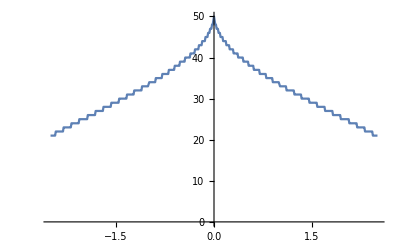

```mathematica
ListPlot[pris,Joined->True]
```

```mathematica
device1[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}], μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}], μ14=RandomInteger[{1,m}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp,imp,imp,imp3}]};
sl1= Module[{J=LEFT[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
device1[1,0.5,50]
```

11.3233

```mathematica
Table[{ω,Mean[Table[device1[ω,0.5,50],2000]]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,20.9478},{-2.49,20.9506},{-2.48,20.9523},{-2.47,20.9532},{-2.46,20.9527},{-2.45,20.9494},{-2.44,20.9385},{-2.43,20.8203},{-2.42,21.8653},{-2.41,21.9163},{-2.4,21.9332},{-2.39,21.9406},{-2.38,21.9451},{-2.37,21.9482},{-2.36,21.9495},{-2.35,21.9503},{-2.34,21.9496},{-2.33,21.9472},{-2.32,21.9363},{-2.31,21.8546},{-2.3,22.8396},{-2.29,22.9095},{-2.28,22.9275},{-2.27,22.9357},{-2.26,22.9407},{-2.25,22.9441},{-2.24,22.9463},{-2.23,22.9471},{-2.22,22.9469},{-2.21,22.9445},{-2.2,22.9365},{-2.19,22.8915},{-2.18,23.7762},{-2.17,23.8953},{-2.16,23.92},{-2.15,23.9303},{-2.14,23.9362},{-2.13,23.9402},{-2.12,23.9423},{-2.11,23.9436},{-2.1,23.9438},{-2.09,23.9417},{-2.08,23.9356},{-2.07,23.9109},{-2.06,24.4728},{-2.05,24.8733},{-2.04,24.9091},{-2.03,24.9227},{-2.02,24.9307},{-2.01,24.9352},{-2.,24.938},{-1.99,24.9397},{-1.98,24.94},{-1.97,24.9383},{-1.96,24.9337},{-1.95,24.9179},{-1.94,24.6944},{-1.93,25.8338},{-1.92,25.895},{-1.91,25.9134},{-1.9,25.9235},{-1.89,25.9289},{-1.88,25.9323},{-1.87,25.9343},{-1.86,25.9354},{-1.85,25.9346},{-1.84,25.9309},{-1.83,25.9185},{-1.82,25.847},{-1.81,26.759},{-1.8,26.877},{-1.79,26.9031},{-1.78,26.9147},{-1.77,26.9223},{-1.76,26.9261},{-1.75,26.9294},{-1.74,26.9306},{-1.73,26.9302},{-1.72,26.9266},{-1.71,26.9182},{-1.7,26.8724},{-1.69,27.6212},{-1.68,27.8563},{-1.67,27.8924},{-1.66,27.9067},{-1.65,27.915},{-1.64,27.9201},{-1.63,27.9231},{-1.62,27.9245},{-1.61,27.9249},{-1.6,27.9215},{-1.59,27.9129},{-1.58,27.8733},{-1.57,28.4482},{-1.56,28.8389},{-1.55,28.8806},{-1.54,28.898},{-1.53,28.9078},{-1.52,28.9127},{-1.51,28.9169},{-1.5,28.9185},{-1.49,28.9179},{-1.48,28.9147},{-1.47,28.9045},{-1.46,28.8584},{-1.45,29.5047},{-1.44,29.8297},{-1.43,29.8735},{-1.42,29.8919},{-1.41,29.9002},{-1.4,29.9061},{-1.39,29.9088},{-1.38,29.9113},{-1.37,29.9097},{-1.36,29.905},{-1.35,29.8894},{-1.34,29.7932},{-1.33,30.6797},{-1.32,30.8348},{-1.31,30.87},{-1.3,30.8857},{-1.29,30.8943},{-1.28,30.8994},{-1.27,30.9026},{-1.26,30.9029},{-1.25,30.9003},{-1.24,30.8905},{-1.23,30.8538},{-1.22,29.7999},{-1.21,31.7794},{-1.2,31.8451},{-1.19,31.869},{-1.18,31.8814},{-1.17,31.889},{-1.16,31.8915},{-1.15,31.8931},{-1.14,31.8922},{-1.13,31.8837},{-1.12,31.8547},{-1.11,31.4432},{-1.1,32.7306},{-1.09,32.8236},{-1.08,32.8541},{-1.07,32.869},{-1.06,32.8767},{-1.05,32.8795},{-1.04,32.8825},{-1.03,32.8794},{-1.02,32.8691},{-1.01,32.8302},{-1.,29.2832},{-0.99,33.7349},{-0.98,33.8162},{-0.97,33.8439},{-0.96,33.8581},{-0.95,33.8659},{-0.94,33.8687},{-0.93,33.8684},{-0.92,33.8628},{-0.91,33.842},{-0.9,33.7117},{-0.89,34.561},{-0.88,34.7722},{-0.87,34.8162},{-0.86,34.8382},{-0.85,34.8469},{-0.84,34.8526},{-0.83,34.8541},{-0.82,34.8488},{-0.81,34.8279},{-0.8,34.7034},{-0.79,35.4927},{-0.78,35.7441},{-0.77,35.7965},{-0.76,35.8202},{-0.75,35.8293},{-0.74,35.8352},{-0.73,35.835},{-0.72,35.8246},{-0.71,35.7813},{-0.7,35.0988},{-0.69,36.629},{-0.68,36.748},{-0.67,36.7875},{-0.66,36.8043},{-0.65,36.8126},{-0.64,36.813},{-0.63,36.8048},{-0.62,36.767},{-0.61,36.3605},{-0.6,37.5536},{-0.59,37.7124},{-0.58,37.7603},{-0.57,37.7785},{-0.56,37.7861},{-0.55,37.7858},{-0.54,37.7683},{-0.53,37.6822},{-0.52,37.7234},{-0.51,38.6166},{-0.5,38.7082},{-0.49,38.7388},{-0.48,38.7527},{-0.47,38.7524},{-0.46,38.7345},{-0.45,38.645},{-0.44,38.5274},{-0.43,39.5656},{-0.42,39.6661},{-0.41,39.7004},{-0.4,39.7144},{-0.39,39.7057},{-0.38,39.6566},{-0.37,39.1365},{-0.36,40.3759},{-0.35,40.5874},{-0.34,40.6413},{-0.33,40.658},{-0.32,40.6494},{-0.31,40.5732},{-0.3,37.8164},{-0.29,41.3685},{-0.28,41.5376},{-0.27,41.5847},{-0.26,41.5814},{-0.25,41.5258},{-0.24,40.7469},{-0.23,42.1956},{-0.22,42.4367},{-0.21,42.4882},{-0.2,42.4745},{-0.19,42.2938},{-0.18,42.2992},{-0.17,43.2369},{-0.16,43.3449},{-0.15,43.3243},{-0.14,42.9747},{-0.13,43.5467},{-0.12,44.0938},{-0.11,44.1368},{-0.1,43.8266},{-0.09,43.9584},{-0.08,44.784},{-0.07,44.6984},{-0.06,35.8568},{-0.05,45.1738},{-0.04,44.8071},{-0.03,44.244},{-0.02,44.4006},{-0.01,42.9673},{0.,36.964},{0.01,40.9744},{0.02,41.9856},{0.03,43.195},{0.04,43.2623},{0.05,44.4221},{0.06,32.0841},{0.07,43.8811},{0.08,44.2735},{0.09,43.3425},{0.1,42.7054},{0.11,43.6626},{0.12,43.7121},{0.13,43.0561},{0.14,41.8216},{0.15,42.9183},{0.16,43.0343},{0.17,42.9276},{0.18,41.8015},{0.19,41.5988},{0.2,42.1624},{0.21,42.2339},{0.22,42.2022},{0.23,41.9011},{0.24,37.5916},{0.25,41.1599},{0.26,41.3431},{0.27,41.3743},{0.28,41.3314},{0.29,41.1281},{0.3,24.6174},{0.31,40.2232},{0.32,40.4321},{0.33,40.4733},{0.34,40.4734},{0.35,40.405},{0.36,40.1254},{0.37,37.1208},{0.38,39.3845},{0.39,39.5299},{0.4,39.5547},{0.41,39.5507},{0.42,39.5116},{0.43,39.3871},{0.44,38.0134},{0.45,38.267},{0.46,38.5496},{0.47,38.6058},{0.48,38.6241},{0.49,38.6102},{0.5,38.568},{0.51,38.4578},{0.52,37.3057},{0.53,37.3436},{0.54,37.6014},{0.55,37.6531},{0.56,37.6685},{0.57,37.6677},{0.58,37.6462},{0.59,37.5839},{0.6,37.3818},{0.61,34.6675},{0.62,36.5643},{0.63,36.6718},{0.64,36.7019},{0.65,36.7099},{0.66,36.7039},{0.67,36.6858},{0.68,36.6333},{0.69,36.4763},{0.7,30.6936},{0.71,35.5783},{0.72,35.7006},{0.73,35.7307},{0.74,35.7426},{0.75,35.7393},{0.76,35.7294},{0.77,35.7012},{0.78,35.6296},{0.79,35.2914},{0.8,34.2781},{0.81,34.6865},{0.82,34.7457},{0.83,34.7638},{0.84,34.7704},{0.85,34.7674},{0.86,34.7537},{0.87,34.7286},{0.88,34.6683},{0.89,34.3932},{0.9,33.2649},{0.91,33.7083},{0.92,33.7655},{0.93,33.7882},{0.94,33.7935},{0.95,33.7925},{0.96,33.7831},{0.97,33.7663},{0.98,33.7269},{0.99,33.6208},{1.,16.617},{1.01,32.6586},{1.02,32.7696},{1.03,32.8004},{1.04,32.8105},{1.05,32.8121},{1.06,32.8099},{1.07,32.7997},{1.08,32.7819},{1.09,32.7416},{1.1,32.617},{1.11,28.9776},{1.12,31.71},{1.13,31.7946},{1.14,31.819},{1.15,31.828},{1.16,31.8291},{1.17,31.8265},{1.18,31.8181},{1.19,31.8039},{1.2,31.7719},{1.21,31.6847},{1.22,28.8674},{1.23,30.6934},{1.24,30.8038},{1.25,30.8313},{1.26,30.8414},{1.27,30.8445},{1.28,30.8433},{1.29,30.8366},{1.3,30.8252},{1.31,30.8049},{1.32,30.7579},{1.33,30.5498},{1.34,29.4516},{1.35,29.7913},{1.36,29.8355},{1.37,29.8513},{1.38,29.8554},{1.39,29.8561},{1.4,29.8525},{1.41,29.8469},{1.42,29.836},{1.43,29.811},{1.44,29.7505},{1.45,29.3145},{1.46,28.6735},{1.47,28.8243},{1.48,28.8519},{1.49,28.8627},{1.5,28.8674},{1.51,28.8672},{1.52,28.8639},{1.53,28.858},{1.54,28.8438},{1.55,28.8203},{1.56,28.7638},{1.57,28.2163},{1.58,27.7141},{1.59,27.8395},{1.6,27.863},{1.61,27.8729},{1.62,27.8771},{1.63,27.8761},{1.64,27.8742},{1.65,27.868},{1.66,27.8577},{1.67,27.8366},{1.68,27.7861},{1.69,27.4742},{1.7,26.6991},{1.71,26.8443},{1.72,26.8708},{1.73,26.8817},{1.74,26.8843},{1.75,26.8851},{1.76,26.8825},{1.77,26.8772},{1.78,26.8693},{1.79,26.8508},{1.8,26.8144},{1.81,26.6563},{1.82,25.5617},{1.83,25.8414},{1.84,25.8773},{1.85,25.8873},{1.86,25.8925},{1.87,25.8926},{1.88,25.891},{1.89,25.8862},{1.9,25.8803},{1.91,25.8678},{1.92,25.8409},{1.93,25.7585},{1.94,23.4021},{1.95,24.8292},{1.96,24.8782},{1.97,24.8926},{1.98,24.8979},{1.99,24.8991},{2.,24.8974},{2.01,24.8946},{2.02,24.889},{2.03,24.8789},{2.04,24.8587},{2.05,24.8071},{2.06,24.229},{2.07,23.7908},{2.08,23.8779},{2.09,23.8966},{2.1,23.903},{2.11,23.906},{2.12,23.9054},{2.13,23.9023},{2.14,23.8978},{2.15,23.89},{2.16,23.8741},{2.17,23.8394},{2.18,23.6765},{2.19,22.7105},{2.2,22.8741},{2.21,22.8992},{2.22,22.9074},{2.23,22.9101},{2.24,22.9106},{2.25,22.9085},{2.26,22.9042},{2.27,22.8967},{2.28,22.8855},{2.29,22.8592},{2.3,22.7624},{2.31,21.5101},{2.32,21.8716},{2.33,21.9026},{2.34,21.9122},{2.35,21.9144},{2.36,21.9159},{2.37,21.9139},{2.38,21.9104},{2.39,21.9037},{2.4,21.8932},{2.41,21.8714},{2.42,21.7976},{2.43,20.189},{2.44,20.8723},{2.45,20.9052},{2.46,20.9156},{2.47,20.9195},{2.48,20.9197},{2.49,20.9186},{2.5,20.915}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/1per.dat",%33]
```

/home/shardulmukim/PhD/fwi/sq_lattice/50sq/1per.dat

```mathematica
device2[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}], μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}], μ14=RandomInteger[{1,m}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp4,imp5,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
devi2= Compile[{ω},device2[ω,0.5,50],CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
Mean[ParallelTable[devi2[0],2000]]//Timing
```

{1.97646,25.8285}

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/2per.dat",%64]
```

/home/shardulmukim/PhD/fwi/sq_lattice/50sq/2per.dat

```mathematica
Table[{ω,Mean[ParallelTable[devi2[ω],2000]]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,20.8655},{-2.49,20.8738},{-2.48,20.8787},{-2.47,20.8819},{-2.46,20.8819},{-2.45,20.8759},{-2.44,20.8544},{-2.43,20.655},{-2.42,21.639},{-2.41,21.7803},{-2.4,21.8225},{-2.39,21.8448},{-2.38,21.859},{-2.37,21.8672},{-2.36,21.8722},{-2.35,21.875},{-2.34,21.8755},{-2.33,21.8694},{-2.32,21.8488},{-2.31,21.7063},{-2.3,22.5836},{-2.29,22.7577},{-2.28,22.809},{-2.27,22.8337},{-2.26,22.8495},{-2.25,22.8582},{-2.24,22.8643},{-2.23,22.8674},{-2.22,22.8679},{-2.21,22.8633},{-2.2,22.8467},{-2.19,22.7651},{-2.18,23.4294},{-2.17,23.7235},{-2.16,23.7885},{-2.15,23.8193},{-2.14,23.837},{-2.13,23.8476},{-2.12,23.8547},{-2.11,23.8589},{-2.1,23.86},{-2.09,23.8564},{-2.08,23.8445},{-2.07,23.7951},{-2.06,23.8279},{-2.05,24.6673},{-2.04,24.7628},{-2.03,24.802},{-2.02,24.821},{-2.01,24.835},{-2.,24.8424},{-1.99,24.8477},{-1.98,24.8502},{-1.97,24.8477},{-1.96,24.8391},{-1.95,24.8069},{-1.94,24.4523},{-1.93,25.5692},{-1.92,25.7248},{-1.91,25.7743},{-1.9,25.8022},{-1.89,25.8178},{-1.88,25.8283},{-1.87,25.8339},{-1.86,25.837},{-1.85,25.8377},{-1.84,25.8301},{-1.83,25.806},{-1.82,25.6753},{-1.81,26.3976},{-1.8,26.6792},{-1.79,26.7481},{-1.78,26.7825},{-1.77,26.8009},{-1.76,26.8131},{-1.75,26.8207},{-1.74,26.8253},{-1.73,26.8243},{-1.72,26.8198},{-1.71,26.7996},{-1.7,26.7155},{-1.69,27.0951},{-1.68,27.6251},{-1.67,27.7195},{-1.66,27.7599},{-1.65,27.7823},{-1.64,27.7964},{-1.63,27.805},{-1.62,27.8102},{-1.61,27.8113},{-1.6,27.8067},{-1.59,27.789},{-1.58,27.7129},{-1.57,27.7604},{-1.56,28.5798},{-1.55,28.6951},{-1.54,28.7389},{-1.53,28.7641},{-1.52,28.7806},{-1.51,28.7883},{-1.5,28.7944},{-1.49,28.7957},{-1.48,28.7901},{-1.47,28.7674},{-1.46,28.6791},{-1.45,28.8504},{-1.44,29.5602},{-1.43,29.6769},{-1.42,29.7212},{-1.41,29.7471},{-1.4,29.7641},{-1.39,29.7716},{-1.38,29.7761},{-1.37,29.7763},{-1.36,29.7679},{-1.35,29.7359},{-1.34,29.5661},{-1.33,30.2086},{-1.32,30.5749},{-1.31,30.6688},{-1.3,30.7077},{-1.29,30.7307},{-1.28,30.7462},{-1.27,30.7537},{-1.26,30.7577},{-1.25,30.7527},{-1.24,30.7349},{-1.23,30.6673},{-1.22,28.6566},{-1.21,31.4374},{-1.2,31.6059},{-1.19,31.6663},{-1.18,31.6964},{-1.17,31.7159},{-1.16,31.7279},{-1.15,31.7329},{-1.14,31.7314},{-1.13,31.7142},{-1.12,31.6589},{-1.11,31.0203},{-1.1,32.3261},{-1.09,32.5534},{-1.08,32.627},{-1.07,32.6677},{-1.06,32.6874},{-1.05,32.6992},{-1.04,32.706},{-1.03,32.7022},{-1.02,32.6826},{-1.01,32.605},{-1.,29.0792},{-0.99,33.3344},{-0.98,33.5269},{-0.97,33.6005},{-0.96,33.6381},{-0.95,33.6597},{-0.94,33.6723},{-0.93,33.6736},{-0.92,33.6614},{-0.91,33.621},{-0.9,33.3896},{-0.89,33.9535},{-0.88,34.4191},{-0.87,34.5334},{-0.86,34.5868},{-0.85,34.6161},{-0.84,34.6324},{-0.83,34.6364},{-0.82,34.6267},{-0.81,34.5834},{-0.8,34.3598},{-0.79,34.7789},{-0.78,35.3543},{-0.77,35.4859},{-0.76,35.5423},{-0.75,35.5718},{-0.74,35.5875},{-0.73,35.5905},{-0.72,35.5691},{-0.71,35.4888},{-0.7,34.4511},{-0.69,36.0765},{-0.68,36.363},{-0.67,36.46},{-0.66,36.5074},{-0.65,36.5302},{-0.64,36.5353},{-0.63,36.5184},{-0.62,36.4433},{-0.61,35.7749},{-0.6,36.916},{-0.59,37.2744},{-0.58,37.3939},{-0.57,37.4465},{-0.56,37.466},{-0.55,37.4674},{-0.54,37.4357},{-0.53,37.2698},{-0.52,36.3575},{-0.51,38.0362},{-0.5,38.2632},{-0.49,38.3428},{-0.48,38.3831},{-0.47,38.3895},{-0.46,38.3527},{-0.45,38.1796},{-0.44,36.9562},{-0.43,38.9168},{-0.42,39.1586},{-0.41,39.2501},{-0.4,39.2842},{-0.39,39.2811},{-0.38,39.1835},{-0.37,38.3098},{-0.36,39.5031},{-0.35,39.9715},{-0.34,40.0979},{-0.33,40.1505},{-0.32,40.138},{-0.31,39.9984},{-0.3,36.4582},{-0.29,40.4513},{-0.28,40.8442},{-0.27,40.9598},{-0.26,40.9779},{-0.25,40.8668},{-0.24,39.576},{-0.23,41.0617},{-0.22,41.6043},{-0.21,41.7257},{-0.2,41.7123},{-0.19,41.3747},{-0.18,40.3419},{-0.17,42.1428},{-0.16,42.3977},{-0.15,42.3638},{-0.14,41.745},{-0.13,41.638},{-0.12,42.7956},{-0.11,42.8966},{-0.1,42.3463},{-0.09,41.434},{-0.08,43.0649},{-0.07,42.9851},{-0.06,31.1048},{-0.05,42.6874},{-0.04,42.1494},{-0.03,39.8607},{-0.02,40.1717},{-0.01,36.399},{0.,25.8117},{0.01,29.5312},{0.02,29.9185},{0.03,37.4249},{0.04,35.644},{0.05,40.7693},{0.06,26.5315},{0.07,40.0559},{0.08,41.7018},{0.09,40.2479},{0.1,37.5866},{0.11,41.5276},{0.12,41.8426},{0.13,40.6855},{0.14,36.4339},{0.15,41.1058},{0.16,41.5844},{0.17,41.4507},{0.18,39.438},{0.19,38.5564},{0.2,40.7766},{0.21,41.0938},{0.22,41.0405},{0.23,40.4918},{0.24,21.593},{0.25,39.6675},{0.26,40.3186},{0.27,40.4489},{0.28,40.3868},{0.29,39.9753},{0.3,27.9129},{0.31,38.7415},{0.32,39.5162},{0.33,39.6884},{0.34,39.6955},{0.35,39.5712},{0.36,39.0368},{0.37,24.7741},{0.38,38.2708},{0.39,38.7708},{0.4,38.8895},{0.41,38.8969},{0.42,38.8276},{0.43,38.5652},{0.44,36.2804},{0.45,36.7554},{0.46,37.8094},{0.47,38.0032},{0.48,38.0548},{0.49,38.0413},{0.5,37.9662},{0.51,37.7255},{0.52,35.7389},{0.53,35.8884},{0.54,36.9334},{0.55,37.122},{0.56,37.1747},{0.57,37.1751},{0.58,37.1347},{0.59,37.0074},{0.6,36.5775},{0.61,23.7151},{0.62,35.7628},{0.63,36.1459},{0.64,36.2502},{0.65,36.2784},{0.66,36.2706},{0.67,36.2336},{0.68,36.1263},{0.69,35.7914},{0.7,20.9241},{0.71,34.7813},{0.72,35.2123},{0.73,35.3199},{0.74,35.3588},{0.75,35.3544},{0.76,35.3377},{0.77,35.2739},{0.78,35.1183},{0.79,34.4593},{0.8,32.281},{0.81,34.1282},{0.82,34.3422},{0.83,34.4071},{0.84,34.4241},{0.85,34.4275},{0.86,34.4022},{0.87,34.3452},{0.88,34.2107},{0.89,33.6498},{0.9,31.0232},{0.91,33.1937},{0.92,33.3975},{0.93,33.4624},{0.94,33.4839},{0.95,33.4869},{0.96,33.4703},{0.97,33.4298},{0.98,33.3481},{0.99,33.1169},{1.,22.3675},{1.01,31.9511},{1.02,32.3959},{1.03,32.4914},{1.04,32.5265},{1.05,32.5346},{1.06,32.5264},{1.07,32.5139},{1.08,32.4681},{1.09,32.381},{1.1,32.1084},{1.11,18.547},{1.12,31.1548},{1.13,31.4614},{1.14,31.5385},{1.15,31.5711},{1.16,31.5782},{1.17,31.5718},{1.18,31.5549},{1.19,31.5208},{1.2,31.4486},{1.21,31.252},{1.22,27.7335},{1.23,30.0607},{1.24,30.4824},{1.25,30.5737},{1.26,30.6034},{1.27,30.6127},{1.28,30.6134},{1.29,30.5999},{1.3,30.5766},{1.31,30.5267},{1.32,30.4184},{1.33,29.9763},{1.34,27.6574},{1.35,29.4236},{1.36,29.5748},{1.37,29.6215},{1.38,29.6402},{1.39,29.6443},{1.4,29.6415},{1.41,29.6246},{1.42,29.5947},{1.43,29.5419},{1.44,29.4087},{1.45,28.5664},{1.46,27.894},{1.47,28.5198},{1.48,28.6225},{1.49,28.6576},{1.5,28.6687},{1.51,28.673},{1.52,28.6641},{1.53,28.6495},{1.54,28.6216},{1.55,28.5678},{1.56,28.4276},{1.57,27.4541},{1.58,27.0585},{1.59,27.5586},{1.6,27.6505},{1.61,27.6815},{1.62,27.6946},{1.63,27.694},{1.64,27.6897},{1.65,27.6758},{1.66,27.6484},{1.67,27.5997},{1.68,27.4905},{1.69,26.8618},{1.7,25.9297},{1.71,26.5754},{1.72,26.6715},{1.73,26.7016},{1.74,26.714},{1.75,26.7167},{1.76,26.7109},{1.77,26.7004},{1.78,26.6796},{1.79,26.6382},{1.8,26.5514},{1.81,26.2192},{1.82,24.1226},{1.83,25.5559},{1.84,25.6799},{1.85,25.7183},{1.86,25.7304},{1.87,25.7348},{1.88,25.7319},{1.89,25.7231},{1.9,25.7053},{1.91,25.6754},{1.92,25.6117},{1.93,25.4204},{1.94,15.6302},{1.95,24.4986},{1.96,24.6802},{1.97,24.7287},{1.98,24.7453},{1.99,24.75},{2.,24.7499},{2.01,24.7434},{2.02,24.729},{2.03,24.7027},{2.04,24.6571},{2.05,24.5379},{2.06,23.5245},{2.07,23.329},{2.08,23.6694},{2.09,23.7368},{2.1,23.7583},{2.11,23.7665},{2.12,23.7661},{2.13,23.7609},{2.14,23.7507},{2.15,23.7295},{2.16,23.6933},{2.17,23.6104},{2.18,23.2529},{2.19,21.868},{2.2,22.655},{2.21,22.7424},{2.22,22.7687},{2.23,22.7786},{2.24,22.7799},{2.25,22.7767},{2.26,22.7673},{2.27,22.7506},{2.28,22.7187},{2.29,22.655},{2.3,22.4449},{2.31,19.1331},{2.32,21.6294},{2.33,21.7468},{2.34,21.778},{2.35,21.7896},{2.36,21.7919},{2.37,21.7886},{2.38,21.7805},{2.39,21.7647},{2.4,21.7396},{2.41,21.6846},{2.42,21.511},{2.43,15.0983},{2.44,20.6256},{2.45,20.7527},{2.46,20.7898},{2.47,20.8002},{2.48,20.8018},{2.49,20.7984},{2.5,20.7908}}

```mathematica
device3[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}], μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}], μ14=RandomInteger[{1,m}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1},{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2},{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp4,imp5,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
devi3= Compile[{ω},device3[ω,0.5,50],CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/3per.dat",%67]
```

/home/shardulmukim/PhD/fwi/sq_lattice/50sq/3per.dat

```mathematica
Table[{ω,Mean[ParallelTable[devi3[ω],2000]]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,20.8069},{-2.49,20.8205},{-2.48,20.8295},{-2.47,20.8342},{-2.46,20.8341},{-2.45,20.8271},{-2.44,20.8034},{-2.43,20.5883},{-2.42,21.4907},{-2.41,21.6839},{-2.4,21.7452},{-2.39,21.7762},{-2.38,21.7981},{-2.37,21.8111},{-2.36,21.8198},{-2.35,21.8243},{-2.34,21.8253},{-2.33,21.8192},{-2.32,21.7944},{-2.31,21.6358},{-2.3,22.4129},{-2.29,22.6492},{-2.28,22.7251},{-2.27,22.762},{-2.26,22.7836},{-2.25,22.7984},{-2.24,22.8075},{-2.23,22.8131},{-2.22,22.8149},{-2.21,22.81},{-2.2,22.7907},{-2.19,22.695},{-2.18,23.2171},{-2.17,23.6073},{-2.16,23.6985},{-2.15,23.7405},{-2.14,23.7659},{-2.13,23.7834},{-2.12,23.7939},{-2.11,23.8003},{-2.1,23.803},{-2.09,23.7992},{-2.08,23.7856},{-2.07,23.7274},{-2.06,23.5515},{-2.05,24.5249},{-2.04,24.6604},{-2.03,24.7163},{-2.02,24.7463},{-2.01,24.7653},{-2.,24.777},{-1.99,24.7851},{-1.98,24.7899},{-1.97,24.7875},{-1.96,24.7773},{-1.95,24.7397},{-1.94,24.3687},{-1.93,25.3881},{-1.92,25.6102},{-1.91,25.6812},{-1.9,25.7183},{-1.89,25.7421},{-1.88,25.7586},{-1.87,25.7678},{-1.86,25.7726},{-1.85,25.7716},{-1.84,25.7644},{-1.83,25.7367},{-1.82,25.5865},{-1.81,26.1682},{-1.8,26.5402},{-1.79,26.6377},{-1.78,26.6903},{-1.77,26.7167},{-1.76,26.7338},{-1.75,26.7463},{-1.74,26.754},{-1.73,26.7562},{-1.72,26.7489},{-1.71,26.7267},{-1.7,26.6288},{-1.69,26.8117},{-1.68,27.4721},{-1.67,27.6012},{-1.66,27.6579},{-1.65,27.6908},{-1.64,27.7123},{-1.63,27.7242},{-1.62,27.7335},{-1.61,27.7365},{-1.6,27.7291},{-1.59,27.7088},{-1.58,27.6211},{-1.57,27.433},{-1.56,28.4104},{-1.55,28.563},{-1.54,28.6306},{-1.53,28.6653},{-1.52,28.6877},{-1.51,28.7003},{-1.5,28.7104},{-1.49,28.713},{-1.48,28.7075},{-1.47,28.6809},{-1.46,28.5771},{-1.45,28.5294},{-1.44,29.382},{-1.43,29.5386},{-1.42,29.6041},{-1.41,29.6427},{-1.4,29.6638},{-1.39,29.6794},{-1.38,29.687},{-1.37,29.6868},{-1.36,29.6768},{-1.35,29.6419},{-1.34,29.4456},{-1.33,29.9311},{-1.32,30.4021},{-1.31,30.524},{-1.3,30.5887},{-1.29,30.6219},{-1.28,30.6406},{-1.27,30.6559},{-1.26,30.6591},{-1.25,30.6553},{-1.24,30.6325},{-1.23,30.5531},{-1.22,28.5483},{-1.21,31.2143},{-1.2,31.4431},{-1.19,31.5282},{-1.18,31.5735},{-1.17,31.601},{-1.16,31.619},{-1.15,31.6265},{-1.14,31.6243},{-1.13,31.6062},{-1.12,31.5376},{-1.11,30.8582},{-1.1,32.0541},{-1.09,32.3655},{-1.08,32.4773},{-1.07,32.527},{-1.06,32.5601},{-1.05,32.5772},{-1.04,32.5876},{-1.03,32.5843},{-1.02,32.5609},{-1.01,32.4692},{-1.,29.4824},{-0.99,33.0745},{-0.98,33.3383},{-0.97,33.4394},{-0.96,33.4914},{-0.95,33.5232},{-0.94,33.5388},{-0.93,33.5444},{-0.92,33.531},{-0.91,33.4811},{-0.9,33.2101},{-0.89,33.5777},{-0.88,34.1822},{-0.87,34.3462},{-0.86,34.4185},{-0.85,34.4602},{-0.84,34.4807},{-0.83,34.49},{-0.82,34.4792},{-0.81,34.4299},{-0.8,34.1741},{-0.79,34.3761},{-0.78,35.0961},{-0.77,35.2738},{-0.76,35.3574},{-0.75,35.4001},{-0.74,35.4231},{-0.73,35.4251},{-0.72,35.4054},{-0.71,35.3083},{-0.7,34.2244},{-0.69,35.7348},{-0.68,36.1089},{-0.67,36.2417},{-0.66,36.3084},{-0.65,36.3446},{-0.64,36.3533},{-0.63,36.3348},{-0.62,36.244},{-0.61,35.518},{-0.6,36.5232},{-0.59,36.9865},{-0.58,37.1449},{-0.57,37.2167},{-0.56,37.2543},{-0.55,37.259},{-0.54,37.2182},{-0.53,37.0236},{-0.52,35.7189},{-0.51,37.6681},{-0.5,37.9659},{-0.49,38.0775},{-0.48,38.1319},{-0.47,38.1499},{-0.46,38.1033},{-0.45,37.8984},{-0.44,36.2979},{-0.43,38.5113},{-0.42,38.8268},{-0.41,38.9546},{-0.4,38.9924},{-0.39,38.9982},{-0.38,38.8778},{-0.37,37.941},{-0.36,38.9416},{-0.35,39.5625},{-0.34,39.7438},{-0.33,39.8137},{-0.32,39.8048},{-0.31,39.6383},{-0.3,36.2576},{-0.29,39.8974},{-0.28,40.4005},{-0.27,40.5588},{-0.26,40.5756},{-0.25,40.4473},{-0.24,39.0617},{-0.23,40.3868},{-0.22,41.056},{-0.21,41.2353},{-0.2,41.2201},{-0.19,40.8392},{-0.18,39.2969},{-0.17,41.4421},{-0.16,41.7838},{-0.15,41.7748},{-0.14,41.0229},{-0.13,40.5717},{-0.12,41.9789},{-0.11,42.1226},{-0.1,41.507},{-0.09,40.1041},{-0.08,42.0197},{-0.07,41.9265},{-0.06,30.4739},{-0.05,41.2288},{-0.04,40.5911},{-0.03,37.5151},{-0.02,37.8227},{-0.01,32.8494},{0.,22.701},{0.01,21.7113},{0.02,20.6986},{0.03,33.8248},{0.04,28.5479},{0.05,38.1825},{0.06,26.1046},{0.07,37.0482},{0.08,40.0067},{0.09,38.5343},{0.1,32.365},{0.11,39.9912},{0.12,40.6506},{0.13,39.4119},{0.14,29.8798},{0.15,39.7774},{0.16,40.6073},{0.17,40.5118},{0.18,38.2845},{0.19,35.3822},{0.2,39.7236},{0.21,40.3049},{0.22,40.302},{0.23,39.6521},{0.24,21.3202},{0.25,38.4284},{0.26,39.5975},{0.27,39.8229},{0.28,39.7624},{0.29,39.2836},{0.3,17.9507},{0.31,37.3861},{0.32,38.8689},{0.33,39.1495},{0.34,39.1989},{0.35,39.0433},{0.36,38.4165},{0.37,19.4456},{0.38,37.3262},{0.39,38.238},{0.4,38.4319},{0.41,38.4598},{0.42,38.3842},{0.43,38.0532},{0.44,35.6257},{0.45,35.1249},{0.46,37.2332},{0.47,37.5895},{0.48,37.6807},{0.49,37.6821},{0.5,37.581},{0.51,37.2703},{0.52,35.1567},{0.53,34.368},{0.54,36.4354},{0.55,36.7525},{0.56,36.8445},{0.57,36.8649},{0.58,36.8029},{0.59,36.6453},{0.6,36.1341},{0.61,19.2018},{0.62,35.0486},{0.63,35.7643},{0.64,35.9346},{0.65,35.9938},{0.66,35.9883},{0.67,35.9374},{0.68,35.8046},{0.69,35.3835},{0.7,22.3598},{0.71,34.043},{0.72,34.8516},{0.73,35.0377},{0.74,35.1033},{0.75,35.1104},{0.76,35.0829},{0.77,34.9975},{0.78,34.8136},{0.79,34.006},{0.8,29.1856},{0.81,33.6875},{0.82,34.0589},{0.83,34.1639},{0.84,34.2036},{0.85,34.2005},{0.86,34.1722},{0.87,34.0982},{0.88,33.9334},{0.89,33.2614},{0.9,27.3189},{0.91,32.7685},{0.92,33.1344},{0.93,33.2412},{0.94,33.279},{0.95,33.2843},{0.96,33.2637},{0.97,33.214},{0.98,33.1098},{0.99,32.8073},{1.,25.15},{1.01,31.2349},{1.02,32.1034},{1.03,32.2757},{1.04,32.3345},{1.05,32.3557},{1.06,32.3477},{1.07,32.3255},{1.08,32.2698},{1.09,32.1532},{1.1,31.8183},{1.11,20.091},{1.12,30.6491},{1.13,31.2131},{1.14,31.3536},{1.15,31.3948},{1.16,31.4121},{1.17,31.4067},{1.18,31.3843},{1.19,31.3366},{1.2,31.244},{1.21,30.9957},{1.22,27.8087},{1.23,29.4462},{1.24,30.2297},{1.25,30.3922},{1.26,30.4425},{1.27,30.4611},{1.28,30.4586},{1.29,30.4466},{1.3,30.4171},{1.31,30.3516},{1.32,30.2138},{1.33,29.6846},{1.34,24.7967},{1.35,29.109},{1.36,29.39},{1.37,29.4685},{1.38,29.497},{1.39,29.5049},{1.4,29.4973},{1.41,29.4794},{1.42,29.4429},{1.43,29.3696},{1.44,29.1997},{1.45,28.241},{1.46,26.9662},{1.47,28.2842},{1.48,28.4562},{1.49,28.5166},{1.5,28.5402},{1.51,28.5428},{1.52,28.5357},{1.53,28.5179},{1.54,28.4791},{1.55,28.4077},{1.56,28.2325},{1.57,27.1443},{1.58,26.3079},{1.59,27.3473},{1.6,27.5011},{1.61,27.5538},{1.62,27.5705},{1.63,27.5782},{1.64,27.5678},{1.65,27.552},{1.66,27.5184},{1.67,27.45},{1.68,27.3045},{1.69,26.5741},{1.7,24.9247},{1.71,26.3603},{1.72,26.5282},{1.73,26.581},{1.74,26.6005},{1.75,26.6077},{1.76,26.6007},{1.77,26.5835},{1.78,26.5577},{1.79,26.5056},{1.8,26.394},{1.81,25.9778},{1.82,21.5099},{1.83,25.3129},{1.84,25.5395},{1.85,25.6016},{1.86,25.626},{1.87,25.6321},{1.88,25.6285},{1.89,25.6168},{1.9,25.5932},{1.91,25.5516},{1.92,25.4659},{1.93,25.2293},{1.94,15.275},{1.95,24.1908},{1.96,24.5329},{1.97,24.6125},{1.98,24.6437},{1.99,24.6527},{2.,24.6527},{2.01,24.6432},{2.02,24.6246},{2.03,24.5912},{2.04,24.5267},{2.05,24.3737},{2.06,23.2655},{2.07,22.811},{2.08,23.5127},{2.09,23.6229},{2.1,23.657},{2.11,23.6749},{2.12,23.6736},{2.13,23.6673},{2.14,23.6519},{2.15,23.628},{2.16,23.5779},{2.17,23.4659},{2.18,23.0329},{2.19,20.5251},{2.2,22.4682},{2.21,22.6281},{2.22,22.6742},{2.23,22.6891},{2.24,22.6943},{2.25,22.6893},{2.26,22.675},{2.27,22.6536},{2.28,22.6121},{2.29,22.5291},{2.3,22.2568},{2.31,14.8836},{2.32,21.4306},{2.33,21.6336},{2.34,21.6861},{2.35,21.7054},{2.36,21.709},{2.37,21.7063},{2.38,21.6958},{2.39,21.6751},{2.4,21.6413},{2.41,21.5638},{2.42,21.3441},{2.43,13.1837},{2.44,20.4009},{2.45,20.643},{2.46,20.6991},{2.47,20.7195},{2.48,20.7251},{2.49,20.7208},{2.5,20.7112}}

```mathematica
device4[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}], μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}], μ14=RandomInteger[{1,m}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1},{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2},{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4},{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5},{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp4,imp5,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
devi4= Compile[{ω},device4[ω,0.5,50],CompilationTarget->"C",RuntimeOptions->"Speed"]
```

CompiledFunction[…]

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/4per.dat",%72]
```

/home/shardulmukim/PhD/fwi/sq_lattice/50sq/4per.dat

```mathematica
Table[{ω,Mean[ParallelTable[devi4[ω],2000]]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,20.7199},{-2.49,20.7381},{-2.48,20.7514},{-2.47,20.7611},{-2.46,20.7631},{-2.45,20.7591},{-2.44,20.7294},{-2.43,20.5126},{-2.42,21.2736},{-2.41,21.5299},{-2.4,21.622},{-2.39,21.6752},{-2.38,21.7032},{-2.37,21.7257},{-2.36,21.7391},{-2.35,21.7479},{-2.34,21.7504},{-2.33,21.745},{-2.32,21.7176},{-2.31,21.5538},{-2.3,22.1737},{-2.29,22.4897},{-2.28,22.5943},{-2.27,22.6491},{-2.26,22.6836},{-2.25,22.7045},{-2.24,22.7213},{-2.23,22.7304},{-2.22,22.7353},{-2.21,22.731},{-2.2,22.7093},{-2.19,22.6052},{-2.18,22.9518},{-2.17,23.4222},{-2.16,23.5548},{-2.15,23.6204},{-2.14,23.6584},{-2.13,23.6839},{-2.12,23.7028},{-2.11,23.7119},{-2.1,23.7181},{-2.09,23.7156},{-2.08,23.7009},{-2.07,23.6366},{-2.06,23.281},{-2.05,24.3145},{-2.04,24.5009},{-2.03,24.58},{-2.02,24.6292},{-2.01,24.6572},{-2.,24.6763},{-1.99,24.6925},{-1.98,24.698},{-1.97,24.6985},{-1.96,24.6868},{-1.95,24.6437},{-1.94,24.2759},{-1.93,25.1418},{-1.92,25.425},{-1.91,25.5304},{-1.9,25.5869},{-1.89,25.624},{-1.88,25.6473},{-1.87,25.6634},{-1.86,25.6716},{-1.85,25.6741},{-1.84,25.6679},{-1.83,25.6361},{-1.82,25.4731},{-1.81,25.8689},{-1.8,26.3346},{-1.79,26.4752},{-1.78,26.5455},{-1.77,26.5881},{-1.76,26.6154},{-1.75,26.6338},{-1.74,26.6466},{-1.73,26.6504},{-1.72,26.645},{-1.71,26.6175},{-1.7,26.5116},{-1.69,26.4806},{-1.68,27.2379},{-1.67,27.418},{-1.66,27.5028},{-1.65,27.5519},{-1.64,27.5826},{-1.63,27.604},{-1.62,27.617},{-1.61,27.6217},{-1.6,27.6186},{-1.59,27.5948},{-1.58,27.4938},{-1.57,27.0945},{-1.56,28.1496},{-1.55,28.3656},{-1.54,28.4585},{-1.53,28.5145},{-1.52,28.5483},{-1.51,28.5721},{-1.5,28.5862},{-1.49,28.5902},{-1.48,28.5851},{-1.47,28.5577},{-1.46,28.4429},{-1.45,28.1638},{-1.44,29.1173},{-1.43,29.3318},{-1.42,29.4269},{-1.41,29.4813},{-1.4,29.5167},{-1.39,29.5373},{-1.38,29.5494},{-1.37,29.5553},{-1.36,29.5454},{-1.35,29.504},{-1.34,29.2914},{-1.33,29.568},{-1.32,30.1367},{-1.31,30.317},{-1.3,30.3959},{-1.29,30.4486},{-1.28,30.4808},{-1.27,30.5047},{-1.26,30.5134},{-1.25,30.5137},{-1.24,30.4878},{-1.23,30.3916},{-1.22,28.6158},{-1.21,30.8932},{-1.2,31.1912},{-1.19,31.315},{-1.18,31.3836},{-1.17,31.428},{-1.16,31.4508},{-1.15,31.4656},{-1.14,31.4659},{-1.13,31.4456},{-1.12,31.3704},{-1.11,30.7057},{-1.1,31.698},{-1.09,32.0938},{-1.08,32.2363},{-1.07,32.3177},{-1.06,32.367},{-1.05,32.3948},{-1.04,32.4079},{-1.03,32.4093},{-1.02,32.3843},{-1.01,32.2818},{-1.,29.9133},{-0.99,32.7041},{-0.98,33.0492},{-0.97,33.1925},{-0.96,33.2649},{-0.95,33.3139},{-0.94,33.3395},{-0.93,33.3505},{-0.92,33.3356},{-0.91,33.2813},{-0.9,32.9945},{-0.89,33.1218},{-0.88,33.839},{-0.87,34.0545},{-0.86,34.1598},{-0.85,34.2232},{-0.84,34.2564},{-0.83,34.2746},{-0.82,34.2662},{-0.81,34.2054},{-0.8,33.9296},{-0.79,33.8712},{-0.78,34.7205},{-0.77,34.9638},{-0.76,35.0766},{-0.75,35.1402},{-0.74,35.1697},{-0.73,35.1832},{-0.72,35.1603},{-0.71,35.053},{-0.7,34.0181},{-0.69,35.2555},{-0.68,35.7286},{-0.67,35.9153},{-0.66,36.0078},{-0.65,36.0591},{-0.64,36.0782},{-0.63,36.0568},{-0.62,35.9578},{-0.61,35.2181},{-0.6,35.9753},{-0.59,36.5723},{-0.58,36.7778},{-0.57,36.881},{-0.56,36.9365},{-0.55,36.9486},{-0.54,36.903},{-0.53,36.6905},{-0.52,35.1745},{-0.51,37.1471},{-0.5,37.5287},{-0.49,37.6873},{-0.48,37.7648},{-0.47,37.7881},{-0.46,37.7469},{-0.45,37.5115},{-0.44,35.7194},{-0.43,37.9264},{-0.42,38.3349},{-0.41,38.5105},{-0.4,38.5818},{-0.39,38.5791},{-0.38,38.4565},{-0.37,37.4806},{-0.36,38.2268},{-0.35,38.9567},{-0.34,39.2165},{-0.33,39.3149},{-0.32,39.3188},{-0.31,39.1281},{-0.3,36.1493},{-0.29,39.1245},{-0.28,39.733},{-0.27,39.9543},{-0.26,39.995},{-0.25,39.8409},{-0.24,38.4478},{-0.23,39.4679},{-0.22,40.2761},{-0.21,40.5132},{-0.2,40.528},{-0.19,40.0897},{-0.18,38.2098},{-0.17,40.4451},{-0.16,40.8778},{-0.15,40.8906},{-0.14,40.1111},{-0.13,39.2504},{-0.12,40.8218},{-0.11,41.0329},{-0.1,40.3481},{-0.09,38.4462},{-0.08,40.5578},{-0.07,40.4545},{-0.06,30.7277},{-0.05,39.2733},{-0.04,38.6587},{-0.03,35.0735},{-0.02,35.1544},{-0.01,29.3216},{0.,19.6081},{0.01,16.32},{0.02,17.1946},{0.03,28.9078},{0.04,16.8946},{0.05,34.2482},{0.06,25.8296},{0.07,31.1739},{0.08,37.2141},{0.09,36.3242},{0.1,20.4991},{0.11,37.2321},{0.12,38.7993},{0.13,37.6914},{0.14,17.7045},{0.15,37.2975},{0.16,39.0746},{0.17,39.1384},{0.18,36.9872},{0.19,27.0917},{0.2,37.9393},{0.21,39.0532},{0.22,39.186},{0.23,38.5717},{0.24,25.0081},{0.25,35.9296},{0.26,38.3917},{0.27,38.8773},{0.28,38.884},{0.29,38.374},{0.3,19.552},{0.31,34.578},{0.32,37.7299},{0.33,38.3345},{0.34,38.4449},{0.35,38.3194},{0.36,37.5938},{0.37,20.4085},{0.38,35.3667},{0.39,37.3088},{0.4,37.7296},{0.41,37.8351},{0.42,37.7596},{0.43,37.398},{0.44,35.0463},{0.45,30.776},{0.46,36.242},{0.47,36.9087},{0.48,37.1116},{0.49,37.13},{0.5,37.0213},{0.51,36.6822},{0.52,34.6353},{0.53,30.3222},{0.54,35.5364},{0.55,36.1515},{0.56,36.3422},{0.57,36.3769},{0.58,36.3368},{0.59,36.1434},{0.6,35.567},{0.61,18.9804},{0.62,33.5263},{0.63,35.0866},{0.64,35.449},{0.65,35.5578},{0.66,35.5708},{0.67,35.5165},{0.68,35.3608},{0.69,34.8752},{0.7,16.7397},{0.71,32.4053},{0.72,34.2384},{0.73,34.5941},{0.74,34.7113},{0.75,34.737},{0.76,34.7147},{0.77,34.6165},{0.78,34.3863},{0.79,33.5185},{0.8,20.0362},{0.81,32.8033},{0.82,33.5795},{0.83,33.7828},{0.84,33.8635},{0.85,33.8696},{0.86,33.8369},{0.87,33.7573},{0.88,33.5411},{0.89,32.7961},{0.9,17.8775},{0.91,31.8983},{0.92,32.6893},{0.93,32.8988},{0.94,32.9725},{0.95,32.9882},{0.96,32.9694},{0.97,32.91},{0.98,32.7744},{0.99,32.4232},{1.,27.6234},{1.01,29.5224},{1.02,31.5978},{1.03,31.9306},{1.04,32.0426},{1.05,32.0797},{1.06,32.0793},{1.07,32.0518},{1.08,31.9841},{1.09,31.8457},{1.1,31.4391},{1.11,16.046},{1.12,29.4457},{1.13,30.7932},{1.14,31.0482},{1.15,31.1317},{1.16,31.1609},{1.17,31.1654},{1.18,31.1404},{1.19,31.0779},{1.2,30.9634},{1.21,30.6601},{1.22,28.0802},{1.23,27.714},{1.24,29.7866},{1.25,30.0939},{1.26,30.1984},{1.27,30.235},{1.28,30.2379},{1.29,30.2257},{1.3,30.1856},{1.31,30.1003},{1.32,29.9276},{1.33,29.3305},{1.34,16.5637},{1.35,28.4773},{1.36,29.0672},{1.37,29.2261},{1.38,29.28},{1.39,29.3004},{1.4,29.2964},{1.41,29.276},{1.42,29.2225},{1.43,29.1306},{1.44,28.9175},{1.45,27.9167},{1.46,23.6036},{1.47,27.8136},{1.48,28.1882},{1.49,28.3024},{1.5,28.3406},{1.51,28.3556},{1.52,28.347},{1.53,28.3231},{1.54,28.2774},{1.55,28.1815},{1.56,27.9621},{1.57,26.8686},{1.58,23.9103},{1.59,26.9453},{1.6,27.2533},{1.61,27.353},{1.62,27.3909},{1.63,27.4016},{1.64,27.3934},{1.65,27.3725},{1.66,27.3298},{1.67,27.2449},{1.68,27.0569},{1.69,26.2729},{1.7,21.2585},{1.71,25.9341},{1.72,26.2899},{1.73,26.3947},{1.74,26.4329},{1.75,26.4441},{1.76,26.4398},{1.77,26.4204},{1.78,26.3792},{1.79,26.3148},{1.8,26.1693},{1.81,25.6888},{1.82,14.5725},{1.83,24.8144},{1.84,25.2979},{1.85,25.4209},{1.86,25.4629},{1.87,25.4792},{1.88,25.4764},{1.89,25.4606},{1.9,25.4349},{1.91,25.3778},{1.92,25.271},{1.93,24.9755},{1.94,13.1098},{1.95,23.425},{1.96,24.2746},{1.97,24.4306},{1.98,24.4892},{1.99,24.5075},{2.,24.5088},{2.01,24.4975},{2.02,24.4721},{2.03,24.43},{2.04,24.3486},{2.05,24.1526},{2.06,23.0662},{2.07,21.0465},{2.08,23.2052},{2.09,23.4354},{2.1,23.5079},{2.11,23.5342},{2.12,23.541},{2.13,23.5348},{2.14,23.5138},{2.15,23.4783},{2.16,23.4134},{2.17,23.2742},{2.18,22.7727},{2.19,15.351},{2.2,22.1047},{2.21,22.4363},{2.22,22.5283},{2.23,22.5584},{2.24,22.567},{2.25,22.563},{2.26,22.5488},{2.27,22.5146},{2.28,22.4658},{2.29,22.3488},{2.3,22.0224},{2.31,12.7238},{2.32,20.9544},{2.33,21.4372},{2.34,21.5442},{2.35,21.5793},{2.36,21.5902},{2.37,21.5878},{2.38,21.5738},{2.39,21.5469},{2.4,21.4963},{2.41,21.3942},{2.42,21.1342},{2.43,11.8978},{2.44,19.8878},{2.45,20.4514},{2.46,20.5643},{2.47,20.5995},{2.48,20.6101},{2.49,20.6073},{2.5,20.5944}}

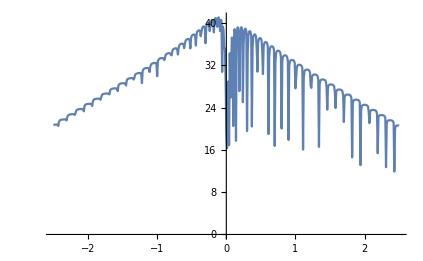

```mathematica
ListPlot[%72,Joined->True]
```

```mathematica
N[50/3]
```

16.6667

```mathematica
device5[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,17}], μ2=RandomInteger[{1,17}], μ3=RandomInteger[{1,17}], μ4=RandomInteger[{1,17}],μ5=RandomInteger[{1,17}], μ6=RandomInteger[{18,34}], μ7=RandomInteger[{18,34}],μ8=RandomInteger[{18,34}], μ9=RandomInteger[{18,34}], μ10=RandomInteger[{18,34}], μ11=RandomInteger[{35,50}],μ12=RandomInteger[{35,50}], μ13=RandomInteger[{35,50}], μ14=RandomInteger[{35,50}],μ15=RandomInteger[{35,50}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1},{μ6,μ6},{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2},{μ7,μ7},{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ8,μ8},{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4},{μ9,μ9},{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5},{μ10,μ10},{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp4,imp5,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
devi5= Compile[{ω},device5[ω,0.5,50],CompilationTarget->"C",RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization" -> True}]
```

CompiledFunction[…]

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/5per.dat",%53]
```

/home/shardulmukim/PhD/fwi/sq_lattice/50sq/5per.dat

```mathematica
Mean[ParallelTable[devi5[0],2000]]//AbsoluteTiming
```

{24.8647,18.4641}

```mathematica
LaunchKernels[6]
```

{KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…],KernelObject[…]}

```mathematica
Table[{ω,Mean[ParallelTable[devi5[ω],2000]]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,20.6554},{-2.49,20.6812},{-2.48,20.6991},{-2.47,20.7102},{-2.46,20.7135},{-2.45,20.7112},{-2.44,20.6827},{-2.43,20.4745},{-2.42,21.1357},{-2.41,21.4267},{-2.4,21.5393},{-2.39,21.6018},{-2.38,21.6382},{-2.37,21.6646},{-2.36,21.6842},{-2.35,21.6939},{-2.34,21.6993},{-2.33,21.6955},{-2.32,21.6671},{-2.31,21.5059},{-2.3,22.0302},{-2.29,22.3775},{-2.28,22.5023},{-2.27,22.5722},{-2.26,22.6161},{-2.25,22.6429},{-2.24,22.6615},{-2.23,22.6751},{-2.22,22.6812},{-2.21,22.679},{-2.2,22.6579},{-2.19,22.5555},{-2.18,22.7943},{-2.17,23.3008},{-2.16,23.4564},{-2.15,23.5321},{-2.14,23.5843},{-2.13,23.6156},{-2.12,23.637},{-2.11,23.6531},{-2.1,23.6609},{-2.09,23.6604},{-2.08,23.6446},{-2.07,23.5799},{-2.06,23.1832},{-2.05,24.1798},{-2.04,24.3922},{-2.03,24.4909},{-2.02,24.5466},{-2.01,24.5819},{-2.,24.6101},{-1.99,24.6276},{-1.98,24.6364},{-1.97,24.6381},{-1.96,24.6271},{-1.95,24.5817},{-1.94,24.2341},{-1.93,24.9877},{-1.92,25.3037},{-1.91,25.431},{-1.9,25.5009},{-1.89,25.5447},{-1.88,25.5709},{-1.87,25.5908},{-1.86,25.6055},{-1.85,25.6092},{-1.84,25.6049},{-1.83,25.5721},{-1.82,25.4112},{-1.81,25.7054},{-1.8,26.1974},{-1.79,26.3621},{-1.78,26.4446},{-1.77,26.5004},{-1.76,26.5342},{-1.75,26.5574},{-1.74,26.5729},{-1.73,26.5809},{-1.72,26.574},{-1.71,26.5499},{-1.7,26.4387},{-1.69,26.3112},{-1.68,27.0871},{-1.67,27.2961},{-1.66,27.3973},{-1.65,27.4528},{-1.64,27.4963},{-1.63,27.52},{-1.62,27.538},{-1.61,27.5465},{-1.6,27.5429},{-1.59,27.5185},{-1.58,27.4186},{-1.57,26.965},{-1.56,27.9902},{-1.55,28.2324},{-1.54,28.3455},{-1.53,28.4123},{-1.52,28.4541},{-1.51,28.4825},{-1.5,28.4996},{-1.49,28.5071},{-1.48,28.5048},{-1.47,28.4744},{-1.46,28.3599},{-1.45,28.0005},{-1.44,28.9539},{-1.43,29.1904},{-1.42,29.3054},{-1.41,29.3721},{-1.4,29.4132},{-1.39,29.4444},{-1.38,29.4598},{-1.37,29.466},{-1.36,29.4581},{-1.35,29.4139},{-1.34,29.2015},{-1.33,29.3583},{-1.32,29.9673},{-1.31,30.1714},{-1.3,30.2734},{-1.29,30.3385},{-1.28,30.3758},{-1.27,30.4028},{-1.26,30.4154},{-1.25,30.4143},{-1.24,30.3921},{-1.23,30.2926},{-1.22,28.7136},{-1.21,30.6982},{-1.2,31.0266},{-1.19,31.1763},{-1.18,31.2546},{-1.17,31.3062},{-1.16,31.3372},{-1.15,31.3581},{-1.14,31.36},{-1.13,31.3418},{-1.12,31.2638},{-1.11,30.635},{-1.1,31.482},{-1.09,31.9095},{-1.08,32.0867},{-1.07,32.175},{-1.06,32.2389},{-1.05,32.2711},{-1.04,32.2912},{-1.03,32.2935},{-1.02,32.2679},{-1.01,32.1638},{-1.,30.1377},{-0.99,32.4787},{-0.98,32.8609},{-0.97,33.0229},{-0.96,33.1203},{-0.95,33.1731},{-0.94,33.2038},{-0.93,33.2191},{-0.92,33.2103},{-0.91,33.1531},{-0.9,32.8592},{-0.89,32.8689},{-0.88,33.6282},{-0.87,33.8696},{-0.86,33.9911},{-0.85,34.0672},{-0.84,34.1079},{-0.83,34.1292},{-0.82,34.1208},{-0.81,34.0629},{-0.8,33.7868},{-0.79,33.6187},{-0.78,34.4829},{-0.77,34.7466},{-0.76,34.8913},{-0.75,34.9626},{-0.74,35.007},{-0.73,35.0213},{-0.72,35.0027},{-0.71,34.8906},{-0.7,33.8958},{-0.69,34.9661},{-0.68,35.4826},{-0.67,35.7006},{-0.66,35.8041},{-0.65,35.8672},{-0.64,35.8891},{-0.63,35.8777},{-0.62,35.7768},{-0.61,35.0538},{-0.6,35.6566},{-0.59,36.3024},{-0.58,36.5408},{-0.57,36.6534},{-0.56,36.7209},{-0.55,36.7387},{-0.54,36.6998},{-0.53,36.4765},{-0.52,34.9342},{-0.51,36.8108},{-0.5,37.2347},{-0.49,37.419},{-0.48,37.5128},{-0.47,37.5417},{-0.46,37.5137},{-0.45,37.2733},{-0.44,35.4606},{-0.43,37.5618},{-0.42,38.0197},{-0.41,38.2101},{-0.4,38.296},{-0.39,38.3023},{-0.38,38.1802},{-0.37,37.2301},{-0.36,37.8004},{-0.35,38.5999},{-0.34,38.8757},{-0.33,38.9873},{-0.32,39.005},{-0.31,38.8127},{-0.3,36.0786},{-0.29,38.657},{-0.28,39.3137},{-0.27,39.5568},{-0.26,39.6215},{-0.25,39.4743},{-0.24,38.123},{-0.23,38.9217},{-0.22,39.7974},{-0.21,40.0582},{-0.2,40.0681},{-0.19,39.6336},{-0.18,37.6547},{-0.17,39.8565},{-0.16,40.3124},{-0.15,40.3264},{-0.14,39.5665},{-0.13,38.4827},{-0.12,40.1009},{-0.11,40.343},{-0.1,39.628},{-0.09,37.6399},{-0.08,39.6589},{-0.07,39.5502},{-0.06,30.8214},{-0.05,38.133},{-0.04,37.4832},{-0.03,33.662},{-0.02,33.5727},{-0.01,27.5639},{0.,18.5037},{0.01,17.8785},{0.02,25.7979},{0.03,25.5286},{0.04,15.1921},{0.05,31.3669},{0.06,25.4652},{0.07,25.8},{0.08,35.236},{0.09,34.9575},{0.1,14.8668},{0.11,35.0744},{0.12,37.5098},{0.13,36.7073},{0.14,14.5958},{0.15,35.315},{0.16,37.9625},{0.17,38.2726},{0.18,36.2989},{0.19,19.6038},{0.2,36.4652},{0.21,38.1723},{0.22,38.4582},{0.23,37.8466},{0.24,19.0157},{0.25,33.4772},{0.26,37.4439},{0.27,38.2128},{0.28,38.3105},{0.29,37.7958},{0.3,23.5303},{0.31,31.4075},{0.32,36.8855},{0.33,37.7253},{0.34,37.9378},{0.35,37.8222},{0.36,37.1269},{0.37,17.9921},{0.38,33.4159},{0.39,36.6377},{0.4,37.2588},{0.41,37.4027},{0.42,37.3389},{0.43,36.9917},{0.44,34.7756},{0.45,25.8949},{0.46,35.4042},{0.47,36.4444},{0.48,36.7259},{0.49,36.7788},{0.5,36.6808},{0.51,36.3186},{0.52,34.3796},{0.53,25.4138},{0.54,34.7365},{0.55,35.7143},{0.56,35.9988},{0.57,36.0621},{0.58,36.0222},{0.59,35.8344},{0.6,35.2222},{0.61,15.9073},{0.62,31.9361},{0.63,34.5858},{0.64,35.0942},{0.65,35.2627},{0.66,35.3031},{0.67,35.2549},{0.68,35.0843},{0.69,34.5772},{0.7,18.1168},{0.71,30.5079},{0.72,33.7393},{0.73,34.2765},{0.74,34.439},{0.75,34.495},{0.76,34.4727},{0.77,34.3751},{0.78,34.1257},{0.79,33.2617},{0.8,14.232},{0.81,31.9502},{0.82,33.2202},{0.83,33.5183},{0.84,33.6234},{0.85,33.6503},{0.86,33.6238},{0.87,33.5308},{0.88,33.3035},{0.89,32.5529},{0.9,13.8203},{0.91,31.032},{0.92,32.3346},{0.93,32.6495},{0.94,32.7572},{0.95,32.7844},{0.96,32.7768},{0.97,32.7112},{0.98,32.5644},{0.99,32.1969},{1.,28.4968},{1.01,27.4967},{1.02,31.1498},{1.03,31.6756},{1.04,31.8371},{1.05,31.8923},{1.06,31.9017},{1.07,31.8774},{1.08,31.8063},{1.09,31.6409},{1.1,31.2282},{1.11,17.2333},{1.12,28.0413},{1.13,30.431},{1.14,30.8222},{1.15,30.9534},{1.16,30.9974},{1.17,31.003},{1.18,30.9791},{1.19,30.9163},{1.2,30.7872},{1.21,30.4661},{1.22,28.2252},{1.23,25.3647},{1.24,29.4066},{1.25,29.8749},{1.26,30.0201},{1.27,30.0793},{1.28,30.0917},{1.29,30.0741},{1.3,30.0352},{1.31,29.9414},{1.32,29.7528},{1.33,29.14},{1.34,13.168},{1.35,27.8447},{1.36,28.8147},{1.37,29.0538},{1.38,29.132},{1.39,29.1602},{1.4,29.1627},{1.41,29.1429},{1.42,29.087},{1.43,28.9823},{1.44,28.7548},{1.45,27.7834},{1.46,19.1828},{1.47,27.4152},{1.48,27.9878},{1.49,28.1498},{1.5,28.2077},{1.51,28.2254},{1.52,28.2225},{1.53,28.1999},{1.54,28.1454},{1.55,28.0437},{1.56,27.8058},{1.57,26.7494},{1.58,20.0926},{1.59,26.5787},{1.6,27.0731},{1.61,27.2145},{1.62,27.2694},{1.63,27.287},{1.64,27.2804},{1.65,27.254},{1.66,27.2052},{1.67,27.1161},{1.68,26.9103},{1.69,26.127},{1.7,16.8378},{1.71,25.5668},{1.72,26.1082},{1.73,26.2597},{1.74,26.3152},{1.75,26.3357},{1.76,26.333},{1.77,26.3143},{1.78,26.2688},{1.79,26.1923},{1.8,26.0352},{1.81,25.5373},{1.82,12.2696},{1.83,24.3014},{1.84,25.1158},{1.85,25.2865},{1.86,25.3525},{1.87,25.3724},{1.88,25.3761},{1.89,25.3624},{1.9,25.3291},{1.91,25.2661},{1.92,25.1466},{1.93,24.8315},{1.94,14.8074},{1.95,22.5334},{1.96,24.0667},{1.97,24.3029},{1.98,24.3806},{1.99,24.4128},{2.,24.4156},{2.01,24.4038},{2.02,24.3786},{2.03,24.3279},{2.04,24.2355},{2.05,24.021},{2.06,22.9936},{2.07,18.5888},{2.08,22.9245},{2.09,23.2998},{2.1,23.4068},{2.11,23.4416},{2.12,23.4507},{2.13,23.4437},{2.14,23.4251},{2.15,23.3815},{2.16,23.3099},{2.17,23.1519},{2.18,22.6404},{2.19,12.4429},{2.2,21.7144},{2.21,22.289},{2.22,22.4248},{2.23,22.4703},{2.24,22.4842},{2.25,22.4833},{2.26,22.4629},{2.27,22.4281},{2.28,22.3657},{2.29,22.2401},{2.3,21.8909},{2.31,12.1871},{2.32,20.4418},{2.33,21.2816},{2.34,21.4388},{2.35,21.4927},{2.36,21.511},{2.37,21.5079},{2.38,21.4957},{2.39,21.4613},{2.4,21.406},{2.41,21.2937},{2.42,21.0046},{2.43,12.1933},{2.44,19.2433},{2.45,20.2871},{2.46,20.4614},{2.47,20.5188},{2.48,20.5361},{2.49,20.5345},{2.5,20.5172}}

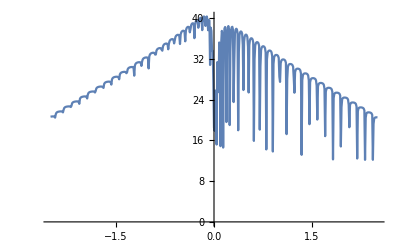

```mathematica
ListPlot[%53,Joined->True]
```

```mathematica
device6[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,17}], μ2=RandomInteger[{1,17}], μ3=RandomInteger[{1,17}], μ4=RandomInteger[{1,17}],μ5=RandomInteger[{1,17}], μ6=RandomInteger[{18,34}], μ7=RandomInteger[{18,34}],μ8=RandomInteger[{18,34}], μ9=RandomInteger[{18,34}], μ10=RandomInteger[{18,34}], μ11=RandomInteger[{35,50}],μ12=RandomInteger[{35,50}], μ13=RandomInteger[{35,50}], μ14=RandomInteger[{35,50}],μ15=RandomInteger[{35,50}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1},{μ6,μ6},{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2},{μ7,μ7},{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ8,μ8},{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4},{μ9,μ9},{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5},{μ10,μ10},{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp4,imp5,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
devi6= Compile[{ω},device6[ω,0.5,50],CompilationTarget->"C",RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization" -> True}]
```

CompiledFunction[…]

```mathematica
Mean[ParallelTable[devi6[0],2000]]//AbsoluteTiming
```

{26.8308,17.42}

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/6per.dat",%61]
```

/home/shardulmukim/PhD/fwi/sq_lattice/50sq/6per.dat

```mathematica
Table[{ω,Mean[ParallelTable[devi6[ω],2000]]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,20.5598},{-2.49,20.5944},{-2.48,20.617},{-2.47,20.6343},{-2.46,20.6434},{-2.45,20.64},{-2.44,20.6125},{-2.43,20.4177},{-2.42,20.9492},{-2.41,21.2718},{-2.4,21.4094},{-2.39,21.4898},{-2.38,21.5378},{-2.37,21.5729},{-2.36,21.5967},{-2.35,21.6145},{-2.34,21.6211},{-2.33,21.6207},{-2.32,21.5957},{-2.31,21.4416},{-2.3,21.8425},{-2.29,22.215},{-2.28,22.3671},{-2.27,22.4547},{-2.26,22.5102},{-2.25,22.5461},{-2.24,22.5718},{-2.23,22.5887},{-2.22,22.5993},{-2.21,22.6012},{-2.2,22.5797},{-2.19,22.4798},{-2.18,22.603},{-2.17,23.125},{-2.16,23.3075},{-2.15,23.4088},{-2.14,23.4691},{-2.13,23.5121},{-2.12,23.5396},{-2.11,23.5612},{-2.1,23.5745},{-2.09,23.5758},{-2.08,23.5614},{-2.07,23.4981},{-2.06,23.0875},{-2.05,23.9863},{-2.04,24.2309},{-2.03,24.3513},{-2.02,24.4193},{-2.01,24.473},{-2.,24.5043},{-1.99,24.5268},{-1.98,24.5445},{-1.97,24.5485},{-1.96,24.5395},{-1.95,24.4947},{-1.94,24.1751},{-1.93,24.7742},{-1.92,25.1207},{-1.91,25.2794},{-1.9,25.3634},{-1.89,25.4201},{-1.88,25.4592},{-1.87,25.4826},{-1.86,25.504},{-1.85,25.5129},{-1.84,25.5075},{-1.83,25.4734},{-1.82,25.3219},{-1.81,25.491},{-1.8,26.0028},{-1.79,26.1928},{-1.78,26.299},{-1.77,26.365},{-1.76,26.4099},{-1.75,26.441},{-1.74,26.4602},{-1.73,26.4741},{-1.72,26.4702},{-1.71,26.4474},{-1.7,26.3378},{-1.69,26.1291},{-1.68,26.8773},{-1.67,27.1096},{-1.66,27.2373},{-1.65,27.3105},{-1.64,27.3595},{-1.63,27.3965},{-1.62,27.4184},{-1.61,27.4296},{-1.6,27.4313},{-1.59,27.4095},{-1.58,27.3085},{-1.57,26.8162},{-1.56,27.7678},{-1.55,28.0359},{-1.54,28.1771},{-1.53,28.2561},{-1.52,28.3084},{-1.51,28.3477},{-1.5,28.3713},{-1.49,28.3887},{-1.48,28.384},{-1.47,28.3556},{-1.46,28.2403},{-1.45,27.8273},{-1.44,28.7114},{-1.43,28.9837},{-1.42,29.122},{-1.41,29.2042},{-1.4,29.2616},{-1.39,29.2973},{-1.38,29.3217},{-1.37,29.3334},{-1.36,29.3246},{-1.35,29.2828},{-1.34,29.0785},{-1.33,29.1182},{-1.32,29.7267},{-1.31,29.9563},{-1.3,30.0827},{-1.29,30.1628},{-1.28,30.2185},{-1.27,30.248},{-1.26,30.2706},{-1.25,30.2741},{-1.24,30.2501},{-1.23,30.156},{-1.22,28.8095},{-1.21,30.4348},{-1.2,30.7874},{-1.19,30.9637},{-1.18,31.0614},{-1.17,31.1292},{-1.16,31.1693},{-1.15,31.1934},{-1.14,31.2011},{-1.13,31.1873},{-1.12,31.1098},{-1.11,30.5259},{-1.1,31.1943},{-1.09,31.6489},{-1.08,31.8474},{-1.07,31.9691},{-1.06,32.0391},{-1.05,32.0896},{-1.04,32.1153},{-1.03,32.1206},{-1.02,32.0974},{-1.01,31.9924},{-1.,30.3361},{-0.99,32.1736},{-0.98,32.5846},{-0.97,32.7792},{-0.96,32.8871},{-0.95,32.9619},{-0.94,33.0063},{-0.93,33.0248},{-0.92,33.0185},{-0.91,32.9623},{-0.9,32.6829},{-0.89,32.5649},{-0.88,33.3137},{-0.87,33.5866},{-0.86,33.7384},{-0.85,33.8299},{-0.84,33.8822},{-0.83,33.9079},{-0.82,33.9104},{-0.81,33.8564},{-0.8,33.5815},{-0.79,33.2876},{-0.78,34.1384},{-0.77,34.4493},{-0.76,34.6114},{-0.75,34.6984},{-0.74,34.7599},{-0.73,34.7841},{-0.72,34.7695},{-0.71,34.6565},{-0.7,33.7494},{-0.69,34.5811},{-0.68,35.131},{-0.67,35.3696},{-0.66,35.5062},{-0.65,35.5885},{-0.64,35.6241},{-0.63,35.6147},{-0.62,35.5094},{-0.61,34.83},{-0.6,35.2576},{-0.59,35.9107},{-0.58,36.1819},{-0.57,36.3271},{-0.56,36.4061},{-0.55,36.4335},{-0.54,36.3982},{-0.53,36.1738},{-0.52,34.708},{-0.51,36.3676},{-0.5,36.8181},{-0.49,37.0411},{-0.48,37.154},{-0.47,37.1971},{-0.46,37.1627},{-0.45,36.9305},{-0.44,35.208},{-0.43,37.0572},{-0.42,37.5422},{-0.41,37.7754},{-0.4,37.8863},{-0.39,37.9024},{-0.38,37.7877},{-0.37,36.8952},{-0.36,37.2502},{-0.35,38.0595},{-0.34,38.3749},{-0.33,38.5132},{-0.32,38.5255},{-0.31,38.3512},{-0.3,35.9728},{-0.29,38.0246},{-0.28,38.7132},{-0.27,38.9876},{-0.26,39.0698},{-0.25,38.9333},{-0.24,37.6604},{-0.23,38.2053},{-0.22,39.071},{-0.21,39.3925},{-0.2,39.4256},{-0.19,39.0042},{-0.18,37.0028},{-0.17,39.0116},{-0.16,39.5299},{-0.15,39.5585},{-0.14,38.7753},{-0.13,37.6076},{-0.12,39.0964},{-0.11,39.3577},{-0.1,38.6742},{-0.09,36.6038},{-0.08,38.4569},{-0.07,38.3627},{-0.06,31.0923},{-0.05,36.6679},{-0.04,35.9809},{-0.03,32.1799},{-0.02,31.9921},{-0.01,25.7886},{0.,18.0679},{0.01,28.9746},{0.02,38.5494},{0.03,19.2103},{0.04,21.6564},{0.05,26.5116},{0.06,24.8989},{0.07,15.9901},{0.08,31.9522},{0.09,33.0213},{0.1,16.0454},{0.11,31.059},{0.12,35.3613},{0.13,35.2787},{0.14,16.3275},{0.15,31.4337},{0.16,36.1629},{0.17,36.9358},{0.18,35.3612},{0.19,12.0406},{0.2,33.5368},{0.21,36.7406},{0.22,37.3435},{0.23,36.9416},{0.24,15.6409},{0.25,28.0417},{0.26,35.7431},{0.27,37.1497},{0.28,37.4481},{0.29,37.037},{0.3,27.7011},{0.31,24.2679},{0.32,35.2495},{0.33,36.7776},{0.34,37.1474},{0.35,37.1253},{0.36,36.5111},{0.37,15.3098},{0.38,28.8654},{0.39,35.338},{0.4,36.4407},{0.41,36.7496},{0.42,36.7574},{0.43,36.3967},{0.44,34.5109},{0.45,16.0122},{0.46,33.6831},{0.47,35.5929},{0.48,36.09},{0.49,36.2281},{0.5,36.1676},{0.51,35.8132},{0.52,34.1033},{0.53,15.899},{0.54,33.1611},{0.55,34.9672},{0.56,35.455},{0.57,35.5818},{0.58,35.5668},{0.59,35.3856},{0.6,34.7943},{0.61,17.2437},{0.62,27.8876},{0.63,33.6091},{0.64,34.5327},{0.65,34.8014},{0.66,34.8894},{0.67,34.8396},{0.68,34.6808},{0.69,34.1814},{0.7,23.5131},{0.71,25.7272},{0.72,32.7876},{0.73,33.7317},{0.74,34.0109},{0.75,34.1203},{0.76,34.117},{0.77,34.0227},{0.78,33.7636},{0.79,32.9342},{0.8,10.752},{0.81,30.0315},{0.82,32.5608},{0.83,33.0835},{0.84,33.2646},{0.85,33.3257},{0.86,33.3087},{0.87,33.2123},{0.88,32.9707},{0.89,32.2509},{0.9,12.0359},{0.91,29.0796},{0.92,31.718},{0.93,32.2493},{0.94,32.4313},{0.95,32.4932},{0.96,32.4936},{0.97,32.4239},{0.98,32.2656},{0.99,31.8904},{1.,29.1078},{1.01,21.0783},{1.02,30.2775},{1.03,31.2349},{1.04,31.5129},{1.05,31.6202},{1.06,31.645},{1.07,31.6176},{1.08,31.5457},{1.09,31.3689},{1.1,30.9448},{1.11,21.9118},{1.12,24.0317},{1.13,29.7126},{1.14,30.4492},{1.15,30.6596},{1.16,30.746},{1.17,30.7658},{1.18,30.7481},{1.19,30.6825},{1.2,30.5321},{1.21,30.1994},{1.22,28.3679},{1.23,18.8454},{1.24,28.6228},{1.25,29.5111},{1.26,29.7516},{1.27,29.8407},{1.28,29.8708},{1.29,29.8675},{1.3,29.8141},{1.31,29.7175},{1.32,29.5166},{1.33,28.9052},{1.34,11.6003},{1.35,26.1829},{1.36,28.3517},{1.37,28.7654},{1.38,28.9031},{1.39,28.9567},{1.4,28.9642},{1.41,28.9437},{1.42,28.8826},{1.43,28.7673},{1.44,28.5198},{1.45,27.62},{1.46,12.1239},{1.47,26.4718},{1.48,27.6213},{1.49,27.9038},{1.5,28.0067},{1.51,28.0409},{1.52,28.0429},{1.53,28.0185},{1.54,27.9588},{1.55,27.8378},{1.56,27.5887},{1.57,26.6282},{1.58,13.117},{1.59,25.7517},{1.6,26.7398},{1.61,26.9867},{1.62,27.0793},{1.63,27.1125},{1.64,27.1099},{1.65,27.0888},{1.66,27.0321},{1.67,26.9315},{1.68,26.7124},{1.69,25.9735},{1.7,10.7826},{1.71,24.6574},{1.72,25.7879},{1.73,26.051},{1.74,26.1404},{1.75,26.1705},{1.76,26.1746},{1.77,26.1576},{1.78,26.1052},{1.79,26.0243},{1.8,25.8446},{1.81,25.3499},{1.82,11.649},{1.83,22.9559},{1.84,24.7485},{1.85,25.0756},{1.86,25.1818},{1.87,25.2226},{1.88,25.2315},{1.89,25.2153},{1.9,25.1792},{1.91,25.1101},{1.92,24.974},{1.93,24.6451},{1.94,18.5054},{1.95,19.633},{1.96,23.6382},{1.97,24.0804},{1.98,24.2165},{1.99,24.2613},{2.,24.2777},{2.01,24.2683},{2.02,24.2395},{2.03,24.179},{2.04,24.0751},{2.05,23.843},{2.06,22.9271},{2.07,12.5815},{2.08,22.3136},{2.09,23.0505},{2.1,23.2381},{2.11,23.2989},{2.12,23.3216},{2.13,23.3178},{2.14,23.2963},{2.15,23.2459},{2.16,23.1626},{2.17,22.9939},{2.18,22.4853},{2.19,10.8855},{2.2,20.7847},{2.21,22.0187},{2.22,22.2531},{2.23,22.3313},{2.24,22.3568},{2.25,22.3602},{2.26,22.3431},{2.27,22.2997},{2.28,22.2301},{2.29,22.0942},{2.3,21.7266},{2.31,12.5234},{2.32,18.8427},{2.33,20.9817},{2.34,21.2699},{2.35,21.3589},{2.36,21.3891},{2.37,21.3945},{2.38,21.3767},{2.39,21.3456},{2.4,21.2782},{2.41,21.1514},{2.42,20.8474},{2.43,14.5945},{2.44,17.1316},{2.45,19.9831},{2.46,20.2952},{2.47,20.386},{2.48,20.4235},{2.49,20.4257},{2.5,20.4078}}

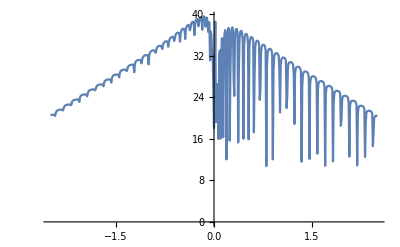

```mathematica
ListPlot[%61,Joined->True]
```

```mathematica
device7[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,13}], μ2=RandomInteger[{1,13}], μ3=RandomInteger[{1,17}], μ4=RandomInteger[{1,17}],μ5=RandomInteger[{1,17}], μ6=RandomInteger[{14,26}], μ7=RandomInteger[{14,26}],μ8=RandomInteger[{18,34}], μ9=RandomInteger[{18,34}], μ10=RandomInteger[{18,34}], μ11=RandomInteger[{27,37}],μ12=RandomInteger[{27,37}], μ13=RandomInteger[{35,50}], μ14=RandomInteger[{35,50}],μ15=RandomInteger[{35,50}],list,b2,μ16=RandomInteger[{38,50}],μ17=RandomInteger[{38,50}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1},{μ6,μ6},{μ11,μ11},{μ16,μ16}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2},{μ7,μ7},{μ12,μ12},{μ17,μ17}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3},{μ8,μ8},{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4},{μ9,μ9},{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5},{μ10,μ10},{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]];
b2=Module[{},list={RandomSample[{imp1,imp2,imp4,imp5,imp3}]};
sl1= Module[{J=SL[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,5}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
devi7= Compile[{ω},device7[ω,0.5,50],CompilationTarget->"C",RuntimeOptions->"Speed",CompilationOptions->{"ExpressionOptimization" -> True},Parallelization->True]
```

CompiledFunction[…]

```mathematica
Mean[ParallelTable[devi7[0],2000]]//AbsoluteTiming
```

{24.4099,17.7807}

```mathematica
Export["/home/shardulmukim/PhD/fwi/sq_lattice/50sq/7per.dat",%30]
```

/home/shardulmukim/PhD/fwi/sq_lattice/50sq/7per.dat

```mathematica
Table[{ω,Mean[ParallelTable[devi7[ω],2000]]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,20.4927},{-2.49,20.5323},{-2.48,20.563},{-2.47,20.582},{-2.46,20.5928},{-2.45,20.5922},{-2.44,20.5662},{-2.43,20.3873},{-2.42,20.8464},{-2.41,21.173},{-2.4,21.3215},{-2.39,21.4096},{-2.38,21.4665},{-2.37,21.5102},{-2.36,21.5393},{-2.35,21.5599},{-2.34,21.5723},{-2.33,21.5703},{-2.32,21.5491},{-2.31,21.4037},{-2.3,21.7337},{-2.29,22.1121},{-2.28,22.2753},{-2.27,22.3715},{-2.26,22.4349},{-2.25,22.4806},{-2.24,22.5109},{-2.23,22.5325},{-2.22,22.5462},{-2.21,22.5475},{-2.2,22.5289},{-2.19,22.4331},{-2.18,22.4992},{-2.17,23.0095},{-2.16,23.2099},{-2.15,23.3206},{-2.14,23.3899},{-2.13,23.4381},{-2.12,23.4736},{-2.11,23.4978},{-2.1,23.5135},{-2.09,23.5189},{-2.08,23.5048},{-2.07,23.4451},{-2.06,23.0417},{-2.05,23.8776},{-2.04,24.1281},{-2.03,24.2572},{-2.02,24.3394},{-2.01,24.3968},{-2.,24.434},{-1.99,24.4619},{-1.98,24.4794},{-1.97,24.4889},{-1.96,24.4798},{-1.95,24.4405},{-1.94,24.1365},{-1.93,24.6593},{-1.92,25.007},{-1.91,25.1777},{-1.9,25.2724},{-1.89,25.3385},{-1.88,25.3778},{-1.87,25.4126},{-1.86,25.4357},{-1.85,25.447},{-1.84,25.445},{-1.83,25.4142},{-1.82,25.2663},{-1.81,25.3803},{-1.8,25.8797},{-1.79,26.0782},{-1.78,26.1985},{-1.77,26.2782},{-1.76,26.3248},{-1.75,26.3641},{-1.74,26.3899},{-1.73,26.4001},{-1.72,26.4041},{-1.71,26.38},{-1.7,26.2733},{-1.69,26.0383},{-1.68,26.7351},{-1.67,26.9886},{-1.66,27.1264},{-1.65,27.2124},{-1.64,27.2695},{-1.63,27.3103},{-1.62,27.3362},{-1.61,27.3571},{-1.6,27.3566},{-1.59,27.3374},{-1.58,27.2363},{-1.57,26.756},{-1.56,27.6267},{-1.55,27.9085},{-1.54,28.06},{-1.53,28.1482},{-1.52,28.2109},{-1.51,28.2542},{-1.5,28.2869},{-1.49,28.304},{-1.48,28.3042},{-1.47,28.2782},{-1.46,28.1651},{-1.45,27.7445},{-1.44,28.5686},{-1.43,28.8503},{-1.42,29.0027},{-1.41,29.0955},{-1.4,29.1573},{-1.39,29.2019},{-1.38,29.2301},{-1.37,29.2453},{-1.36,29.2402},{-1.35,29.2031},{-1.34,29.0051},{-1.33,28.9807},{-1.32,29.5802},{-1.31,29.8249},{-1.3,29.9602},{-1.29,30.0451},{-1.28,30.1029},{-1.27,30.1473},{-1.26,30.1709},{-1.25,30.1754},{-1.24,30.1564},{-1.23,30.0655},{-1.22,28.8673},{-1.21,30.2687},{-1.2,30.6395},{-1.19,30.8218},{-1.18,30.9338},{-1.17,31.0039},{-1.16,31.0576},{-1.15,31.088},{-1.14,31.0995},{-1.13,31.0839},{-1.12,31.0062},{-1.11,30.4647},{-1.1,31.029},{-1.09,31.4879},{-1.08,31.7013},{-1.07,31.827},{-1.06,31.9068},{-1.05,31.9635},{-1.04,31.9977},{-1.03,32.0076},{-1.02,31.9861},{-1.01,31.8852},{-1.,30.4315},{-0.99,31.995},{-0.98,32.4146},{-0.97,32.6119},{-0.96,32.7418},{-0.95,32.8192},{-0.94,32.8735},{-0.93,32.8999},{-0.92,32.8943},{-0.91,32.8412},{-0.9,32.5736},{-0.89,32.3916},{-0.88,33.125},{-0.87,33.4139},{-0.86,33.5737},{-0.85,33.6703},{-0.84,33.734},{-0.83,33.7718},{-0.82,33.7755},{-0.81,33.7188},{-0.8,33.4517},{-0.79,33.1108},{-0.78,33.9379},{-0.77,34.2527},{-0.76,34.4259},{-0.75,34.5315},{-0.74,34.5936},{-0.73,34.6231},{-0.72,34.6129},{-0.71,34.5026},{-0.7,33.6702},{-0.69,34.3626},{-0.68,34.9112},{-0.67,35.1753},{-0.66,35.3095},{-0.65,35.399},{-0.64,35.4411},{-0.63,35.4417},{-0.62,35.3396},{-0.61,34.7038},{-0.6,35.0208},{-0.59,35.6647},{-0.58,35.9533},{-0.57,36.1179},{-0.56,36.1982},{-0.55,36.2284},{-0.54,36.2066},{-0.53,35.9919},{-0.52,34.5921},{-0.51,36.0983},{-0.5,36.5552},{-0.49,36.7808},{-0.48,36.9127},{-0.47,36.9661},{-0.46,36.9366},{-0.45,36.713},{-0.44,35.0692},{-0.43,36.7633},{-0.42,37.2521},{-0.41,37.488},{-0.4,37.6135},{-0.39,37.6394},{-0.38,37.5222},{-0.37,36.6884},{-0.36,36.9174},{-0.35,37.7213},{-0.34,38.0454},{-0.33,38.206},{-0.32,38.2296},{-0.31,38.0395},{-0.3,35.9334},{-0.29,37.6415},{-0.28,38.3319},{-0.27,38.6217},{-0.26,38.7096},{-0.25,38.5796},{-0.24,37.3845},{-0.23,37.7732},{-0.22,38.6329},{-0.21,38.9581},{-0.2,38.9958},{-0.19,38.5873},{-0.18,36.6722},{-0.17,38.501},{-0.16,38.9895},{-0.15,39.0499},{-0.14,38.3045},{-0.13,37.0544},{-0.12,38.516},{-0.11,38.7434},{-0.1,38.0962},{-0.09,36.0063},{-0.08,37.6911},{-0.07,37.6229},{-0.06,31.3067},{-0.05,35.7584},{-0.04,35.0766},{-0.03,31.3541},{-0.02,30.9535},{-0.01,24.8331},{0.,17.4739},{0.01,38.7633},{0.02,41.9638},{0.03,15.1894},{0.04,29.1744},{0.05,22.5188},{0.06,23.9436},{0.07,12.1566},{0.08,29.5153},{0.09,31.6154},{0.1,17.7146},{0.11,27.5572},{0.12,33.8272},{0.13,34.1602},{0.14,15.7784},{0.15,27.842},{0.16,34.673},{0.17,36.0247},{0.18,34.7279},{0.19,10.5354},{0.2,31.1133},{0.21,35.6862},{0.22,36.6082},{0.23,36.2728},{0.24,18.0972},{0.25,23.0041},{0.26,34.4979},{0.27,36.4343},{0.28,36.8117},{0.29,36.4962},{0.3,29.2964},{0.31,18.447},{0.32,33.744},{0.33,36.065},{0.34,36.6241},{0.35,36.6609},{0.36,36.0709},{0.37,18.1929},{0.38,24.7088},{0.39,34.2371},{0.4,35.8271},{0.41,36.2942},{0.42,36.3585},{0.43,36.0209},{0.44,34.3489},{0.45,11.1978},{0.46,32.1757},{0.47,34.9776},{0.48,35.6613},{0.49,35.8651},{0.5,35.8348},{0.51,35.4949},{0.52,33.9487},{0.53,10.5622},{0.54,31.7419},{0.55,34.4037},{0.56,35.0556},{0.57,35.2604},{0.58,35.272},{0.59,35.0963},{0.6,34.5307},{0.61,21.0572},{0.62,23.5426},{0.63,32.788},{0.64,34.09},{0.65,34.4739},{0.66,34.611},{0.67,34.5793},{0.68,34.4306},{0.69,33.9333},{0.7,26.3272},{0.71,20.571},{0.72,31.8869},{0.73,33.3342},{0.74,33.7154},{0.75,33.8648},{0.76,33.8898},{0.77,33.8002},{0.78,33.5484},{0.79,32.7425},{0.8,10.8653},{0.81,28.0516},{0.82,32.0262},{0.83,32.7634},{0.84,33.0188},{0.85,33.106},{0.86,33.1013},{0.87,33.0112},{0.88,32.7695},{0.89,32.0762},{0.9,12.6383},{0.91,26.6582},{0.92,31.2028},{0.93,31.9385},{0.94,32.1992},{0.95,32.2876},{0.96,32.2972},{0.97,32.2429},{0.98,32.0852},{0.99,31.7047},{1.,29.3894},{1.01,15.2351},{1.02,29.4642},{1.03,30.9159},{1.04,31.278},{1.05,31.4168},{1.06,31.4681},{1.07,31.4522},{1.08,31.3717},{1.09,31.2052},{1.1,30.7791},{1.11,24.448},{1.12,19.7834},{1.13,29.0847},{1.14,30.1455},{1.15,30.4554},{1.16,30.5732},{1.17,30.6046},{1.18,30.59},{1.19,30.5191},{1.2,30.3818},{1.21,30.0418},{1.22,28.4559},{1.23,13.779},{1.24,27.8685},{1.25,29.2092},{1.26,29.5489},{1.27,29.6834},{1.28,29.7254},{1.29,29.7194},{1.3,29.6754},{1.31,29.5774},{1.32,29.3594},{1.33,28.7823},{1.34,12.5424},{1.35,24.2422},{1.36,27.9649},{1.37,28.5445},{1.38,28.7423},{1.39,28.817},{1.4,28.8303},{1.41,28.8168},{1.42,28.7566},{1.43,28.6416},{1.44,28.379},{1.45,27.5373},{1.46,9.54},{1.47,25.4081},{1.48,27.328},{1.49,27.726},{1.5,27.8622},{1.51,27.9094},{1.52,27.9219},{1.53,27.8989},{1.54,27.8394},{1.55,27.7152},{1.56,27.4618},{1.57,26.5759},{1.58,9.69559},{1.59,24.912},{1.6,26.4737},{1.61,26.8301},{1.62,26.9491},{1.63,26.998},{1.64,27.003},{1.65,26.9785},{1.66,26.9223},{1.67,26.8127},{1.68,26.5867},{1.69,25.8819},{1.7,9.34374},{1.71,23.603},{1.72,25.5298},{1.73,25.8914},{1.74,26.0164},{1.75,26.0624},{1.76,26.0712},{1.77,26.0514},{1.78,26.0006},{1.79,25.9124},{1.8,25.7287},{1.81,25.2449},{1.82,12.3986},{1.83,21.3144},{1.84,24.4357},{1.85,24.9047},{1.86,25.0627},{1.87,25.1188},{1.88,25.1352},{1.89,25.12},{1.9,25.0822},{1.91,25.0075},{1.92,24.8644},{1.93,24.5374},{1.94,20.2515},{1.95,16.3926},{1.96,23.2272},{1.97,23.9124},{1.98,24.0922},{1.99,24.1616},{2.,24.1857},{2.01,24.177},{2.02,24.1514},{2.03,24.0884},{2.04,23.9761},{2.05,23.7392},{2.06,22.8897},{2.07,9.62217},{2.08,21.6557},{2.09,22.8619},{2.1,23.1137},{2.11,23.1995},{2.12,23.2308},{2.13,23.2338},{2.14,23.2076},{2.15,23.1615},{2.16,23.0718},{2.17,22.8936},{2.18,22.3927},{2.19,10.6935},{2.2,19.4585},{2.21,21.7718},{2.22,22.1285},{2.23,22.2338},{2.24,22.274},{2.25,22.2768},{2.26,22.2632},{2.27,22.2195},{2.28,22.1402},{2.29,21.9973},{2.3,21.6389},{2.31,14.5102},{2.32,16.6853},{2.33,20.6874},{2.34,21.1402},{2.35,21.2645},{2.36,21.3078},{2.37,21.3205},{2.38,21.3045},{2.39,21.2674},{2.4,21.1965},{2.41,21.0661},{2.42,20.755},{2.43,16.4549},{2.44,14.3924},{2.45,19.6777},{2.46,20.1673},{2.47,20.2978},{2.48,20.3425},{2.49,20.3533},{2.5,20.34}}

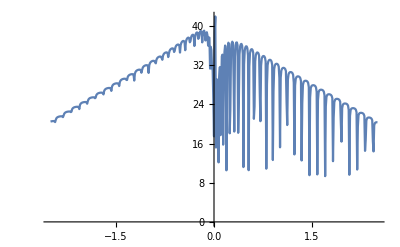

```mathematica
ListPlot[%30,Joined->True]
```

```mathematica
ca16[ω_,ϵ1_,m_]:=Module[{Tin=T[1,m],T1=T[1,m],μ1=RandomInteger[{1,m}], μ2=RandomInteger[{1,m}], μ3=RandomInteger[{1,m}], μ4=RandomInteger[{1,m}],μ5=RandomInteger[{1,m}], μ6=RandomInteger[{1,m}], μ7=RandomInteger[{1,m}],μ8=RandomInteger[{1,m}], μ9=RandomInteger[{1,m}], μ10=RandomInteger[{1,m}], μ11=RandomInteger[{1,m}],μ12=RandomInteger[{1,m}], μ13=RandomInteger[{1,m}], μ14=RandomInteger[{1,m}], μ15=RandomInteger[{1,m}], μ16=RandomInteger[{1,m}],μ17=RandomInteger[{1,m}], μ18=RandomInteger[{1,m}], μ19=RandomInteger[{1,m}],μ20=RandomInteger[{1,m}],μ21=RandomInteger[{1,m}], μ22=RandomInteger[{1,m}], μ23=RandomInteger[{1,m}], μ24=RandomInteger[{1,m}],μ25=RandomInteger[{1,m}], μ26=RandomInteger[{1,m}], μ27=RandomInteger[{1,m}],μ28=RandomInteger[{1,m}], μ29=RandomInteger[{1,m}], μ30=RandomInteger[{1,m}], μ31=RandomInteger[{1,m}],μ32=RandomInteger[{1,m}], μ33=RandomInteger[{1,m}], μ34=RandomInteger[{1,m}], μ35=RandomInteger[{1,m}], μ36=RandomInteger[{1,m}],μ37=RandomInteger[{1,m}], μ38=RandomInteger[{1,m}], μ39=RandomInteger[{1,m}],μ40=RandomInteger[{1,m}],list,b2},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]];
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ16,μ16}}->ω+ⅈ*0.0001-ϵ1]]];imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ17,μ17}}->ω+ⅈ*0.0001-ϵ1]]];
imp18:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ18,μ18}}->ω+ⅈ*0.0001-ϵ1]]];
imp19:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ19,μ19}}->ω+ⅈ*0.0001-ϵ1]]];
imp20:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ20,μ20}}->ω+ⅈ*0.0001-ϵ1]]];imp21:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ21,μ21}}->ω+ⅈ*0.0001-ϵ1]]];
imp22:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ22,μ22}}->ω+ⅈ*0.0001-ϵ1]]];
imp23:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ23,μ23}}->ω+ⅈ*0.0001-ϵ1]]];
imp24:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ24,μ24}}->ω+ⅈ*0.0001-ϵ1]]];
imp25:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ25,μ25}}->ω+ⅈ*0.0001-ϵ1]]];imp26:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ26,μ26}}->ω+ⅈ*0.0001-ϵ1]]];
imp27:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ27,μ27}}->ω+ⅈ*0.0001-ϵ1]]];
imp28:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ28,μ28}}->ω+ⅈ*0.0001-ϵ1]]];
imp29:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ29,μ29}}->ω+ⅈ*0.0001-ϵ1]]];
imp30:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ30,μ30}}->ω+ⅈ*0.0001-ϵ1]]];imp31:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ31,μ31}}->ω+ⅈ*0.0001-ϵ1]]];
imp32:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ32,μ32}}->ω+ⅈ*0.0001-ϵ1]]];
imp33:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ33,μ33}}->ω+ⅈ*0.0001-ϵ1]]];
imp34:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ34,μ34}}->ω+ⅈ*0.0001-ϵ1]]];
imp35:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ35,μ35}}->ω+ⅈ*0.0001-ϵ1]]];
imp36:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ36,μ36}}->ω+ⅈ*0.0001-ϵ1]]];imp37:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ37,μ37}}->ω+ⅈ*0.0001-ϵ1]]];
imp38:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ38,μ38}}->ω+ⅈ*0.0001-ϵ1]]];
imp39:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ39,μ39}}->ω+ⅈ*0.0001-ϵ1]]];
imp40:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{μ40,μ40}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0,m]},ReplacePart[κ,{{10,10}}->ω+ⅈ*0.0001-0]]];
b2=Module[{},list={RandomSample[{imp,imp19,imp27,imp34,imp37,imp15,imp,imp,imp8,imp33,imp,imp22,imp18,imp3,imp9,imp14,imp,imp20,imp10,imp35,imp36,imp30,imp31,imp11,imp38,imp,imp23,imp,imp2,imp,imp26,imp6,imp25,imp1,imp13,imp7,imp28,imp,imp4,imp,imp12,imp17,imp24,imp40,imp32,imp5,imp29,imp39,imp16,imp21}]};
sl1= Module[{J=LEFT[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,50}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
ca16[1,0.5,50]
```

18.2093

```mathematica
ca162[1,0.5,50,0.0001,1,0]
```

18.9451

```mathematica
Mean[ParallelTable[ca16[2.5,0.5,50],5000]]
```

19.6854

```mathematica
Table[{ω,Mean[ParallelTable[ca16[ω,0.5,50],5000]]},{ω,Range[-2.5,2.5,0.01]}]
```

{{-2.5,20.1284},{-2.49,20.1883},{-2.48,20.2349},{-2.47,20.2681},{-2.46,20.2919},{-2.45,20.3145},{-2.44,20.3105},{-2.43,20.158},{-2.42,19.425},{-2.41,20.4997},{-2.4,20.8355},{-2.39,20.9836},{-2.38,21.0765},{-2.37,21.1375},{-2.36,21.1857},{-2.35,21.2187},{-2.34,21.2485},{-2.33,21.2667},{-2.32,21.2672},{-2.31,21.1568},{-2.3,20.2874},{-2.29,21.3537},{-2.28,21.7358},{-2.27,21.9034},{-2.26,22.0085},{-2.25,22.0729},{-2.24,22.1254},{-2.23,22.1649},{-2.22,22.1935},{-2.21,22.2153},{-2.2,22.2222},{-2.19,22.1612},{-2.18,21.3046},{-2.17,22.0869},{-2.16,22.5961},{-2.15,22.8003},{-2.14,22.9225},{-2.13,22.9972},{-2.12,23.0549},{-2.11,23.1},{-2.1,23.1308},{-2.09,23.1563},{-2.08,23.1707},{-2.07,23.1432},{-2.06,22.3451},{-2.05,22.5914},{-2.04,23.4007},{-2.03,23.672},{-2.02,23.8216},{-2.01,23.9122},{-2.,23.9778},{-1.99,24.0274},{-1.98,24.0631},{-1.97,24.0943},{-1.96,24.113},{-1.95,24.1043},{-1.94,23.8354},{-1.93,22.8651},{-1.92,24.1024},{-1.91,24.4977},{-1.9,24.6845},{-1.89,24.7986},{-1.88,24.8741},{-1.87,24.9321},{-1.86,24.976},{-1.85,25.0091},{-1.84,25.0342},{-1.83,25.0389},{-1.82,24.9334},{-1.81,23.7742},{-1.8,24.763},{-1.79,25.3036},{-1.78,25.5383},{-1.77,25.6776},{-1.76,25.7664},{-1.75,25.8364},{-1.74,25.8878},{-1.73,25.9249},{-1.72,25.9545},{-1.71,25.9636},{-1.7,25.905},{-1.69,24.8093},{-1.68,25.3563},{-1.67,26.0967},{-1.66,26.3882},{-1.65,26.5547},{-1.64,26.6567},{-1.63,26.7311},{-1.62,26.7904},{-1.61,26.8355},{-1.6,26.8642},{-1.59,26.8817},{-1.58,26.8335},{-1.57,25.7087},{-1.56,25.9853},{-1.55,26.9022},{-1.54,27.244},{-1.53,27.4285},{-1.52,27.5445},{-1.51,27.625},{-1.5,27.6914},{-1.49,27.7395},{-1.48,27.7709},{-1.47,27.7873},{-1.46,27.728},{-1.45,26.4827},{-1.44,26.8893},{-1.43,27.78},{-1.42,28.1249},{-1.41,28.314},{-1.4,28.4362},{-1.39,28.5196},{-1.38,28.5882},{-1.37,28.6376},{-1.36,28.6704},{-1.35,28.6771},{-1.34,28.5421},{-1.33,26.9722},{-1.32,28.0536},{-1.31,28.7407},{-1.3,29.0433},{-1.29,29.221},{-1.28,29.3359},{-1.27,29.4226},{-1.26,29.4877},{-1.25,29.5315},{-1.24,29.5569},{-1.23,29.5263},{-1.22,28.1853},{-1.21,27.8798},{-1.2,29.2784},{-1.19,29.7496},{-1.18,29.9936},{-1.17,30.1424},{-1.16,30.2488},{-1.15,30.33},{-1.14,30.3822},{-1.13,30.4161},{-1.12,30.4038},{-1.11,29.9202},{-1.1,28.2214},{-1.09,29.9104},{-1.08,30.5023},{-1.07,30.7806},{-1.06,30.9553},{-1.05,31.0727},{-1.04,31.1641},{-1.03,31.2239},{-1.02,31.2625},{-1.01,31.2347},{-1.,29.8051},{-0.99,29.1774},{-0.98,30.775},{-0.97,31.3398},{-0.96,31.6215},{-0.95,31.8},{-0.94,31.9155},{-0.93,32.0031},{-0.92,32.0649},{-0.91,32.0825},{-0.9,31.8999},{-0.89,29.7636},{-0.88,31.0112},{-0.87,31.875},{-0.86,32.2747},{-0.85,32.5106},{-0.84,32.6598},{-0.83,32.7669},{-0.82,32.8419},{-0.81,32.8686},{-0.8,32.7075},{-0.79,30.4536},{-0.78,31.5846},{-0.77,32.548},{-0.76,32.9954},{-0.75,33.2574},{-0.74,33.4176},{-0.73,33.5397},{-0.72,33.6115},{-0.71,33.6006},{-0.7,32.8477},{-0.69,30.6537},{-0.68,32.7146},{-0.67,33.4594},{-0.66,33.8166},{-0.65,34.0567},{-0.64,34.1969},{-0.63,34.3032},{-0.62,34.3157},{-0.61,33.7916},{-0.6,31.0674},{-0.59,33.1652},{-0.58,34.0306},{-0.57,34.4402},{-0.56,34.7028},{-0.55,34.8728},{-0.54,34.9667},{-0.53,34.9011},{-0.52,32.32},{-0.51,32.4891},{-0.5,34.1332},{-0.49,34.8209},{-0.48,35.1749},{-0.47,35.4023},{-0.46,35.5246},{-0.45,35.4687},{-0.44,32.6347},{-0.43,32.7885},{-0.42,34.5703},{-0.41,35.3005},{-0.4,35.6843},{-0.39,35.9209},{-0.38,35.9948},{-0.37,35.3452},{-0.36,31.7822},{-0.35,34.3243},{-0.34,35.4246},{-0.33,35.944},{-0.32,36.2436},{-0.31,36.3087},{-0.3,34.275},{-0.29,32.0802},{-0.28,34.7244},{-0.27,35.7731},{-0.26,36.2484},{-0.25,36.4509},{-0.24,35.5205},{-0.23,31.4368},{-0.22,34.3706},{-0.21,35.6057},{-0.2,36.1666},{-0.19,36.1829},{-0.18,31.5433},{-0.17,32.6583},{-0.16,34.7358},{-0.15,35.561},{-0.14,35.3747},{-0.13,29.661},{-0.12,32.2404},{-0.11,33.969},{-0.1,34.1937},{-0.09,27.6508},{-0.08,29.9332},{-0.07,31.6956},{-0.06,24.3585},{-0.05,24.3147},{-0.04,26.6592},{-0.03,16.5812},{-0.02,16.7072},{-0.01,7.69445},{0.,27.1735},{0.01,24.4076},{0.02,14.3997},{0.03,7.4144},{0.04,8.06716},{0.05,19.4231},{0.06,6.64573},{0.07,21.0664},{0.08,26.0257},{0.09,21.3084},{0.1,15.6665},{0.11,29.2278},{0.12,29.349},{0.13,25.3818},{0.14,17.0544},{0.15,30.9459},{0.16,31.7974},{0.17,30.6799},{0.18,25.3391},{0.19,22.7422},{0.2,32.5141},{0.21,32.9627},{0.22,32.3613},{0.23,30.0155},{0.24,9.63245},{0.25,31.5202},{0.26,33.535},{0.27,33.5371},{0.28,32.9727},{0.29,31.1726},{0.3,11.569},{0.31,30.5628},{0.32,33.6684},{0.33,33.8469},{0.34,33.5687},{0.35,32.8541},{0.36,30.7045},{0.37,12.8822},{0.38,32.1015},{0.39,33.7109},{0.4,33.834},{0.41,33.6043},{0.42,33.1106},{0.43,31.9252},{0.44,26.8341},{0.45,27.1356},{0.46,33.2232},{0.47,33.6006},{0.48,33.5599},{0.49,33.3182},{0.5,32.8348},{0.51,31.7587},{0.52,27.1781},{0.53,26.6802},{0.54,32.8515},{0.55,33.2345},{0.56,33.2249},{0.57,33.0674},{0.58,32.7398},{0.59,32.1333},{0.6,30.414},{0.61,13.2156},{0.62,31.2111},{0.63,32.6306},{0.64,32.7746},{0.65,32.733},{0.66,32.5775},{0.67,32.2665},{0.68,31.7454},{0.69,30.3466},{0.7,11.2551},{0.71,30.1798},{0.72,32.0423},{0.73,32.2189},{0.74,32.1983},{0.75,32.086},{0.76,31.8865},{0.77,31.5391},{0.78,30.8346},{0.79,28.5502},{0.8,22.9866},{0.81,30.9488},{0.82,31.5239},{0.83,31.5999},{0.84,31.5552},{0.85,31.4515},{0.86,31.2502},{0.87,30.9302},{0.88,30.3214},{0.89,28.323},{0.9,22.384},{0.91,30.235},{0.92,30.8379},{0.93,30.9209},{0.94,30.8929},{0.95,30.8075},{0.96,30.6574},{0.97,30.425},{0.98,30.0149},{0.99,29.014},{1.,20.9551},{1.01,27.4775},{1.02,29.9845},{1.03,30.1778},{1.04,30.1982},{1.05,30.1427},{1.06,30.0573},{1.07,29.8962},{1.08,29.6507},{1.09,29.2352},{1.1,28.1043},{1.11,10.9948},{1.12,27.924},{1.13,29.2883},{1.14,29.4285},{1.15,29.4322},{1.16,29.3849},{1.17,29.3046},{1.18,29.1691},{1.19,28.9553},{1.2,28.5961},{1.21,27.7714},{1.22,22.8537},{1.23,25.6929},{1.24,28.4397},{1.25,28.6205},{1.26,28.6474},{1.27,28.615},{1.28,28.5498},{1.29,28.4463},{1.3,28.2854},{1.31,28.029},{1.32,27.5491},{1.33,25.995},{1.34,20.8633},{1.35,27.2864},{1.36,27.7616},{1.37,27.8277},{1.38,27.8222},{1.39,27.7763},{1.4,27.7048},{1.41,27.5977},{1.42,27.4258},{1.43,27.1453},{1.44,26.5703},{1.45,24.3206},{1.46,21.1048},{1.47,26.7028},{1.48,26.9565},{1.49,26.9946},{1.5,26.9749},{1.51,26.9326},{1.52,26.8648},{1.53,26.754},{1.54,26.5868},{1.55,26.3214},{1.56,25.7468},{1.57,23.3855},{1.58,21.1119},{1.59,25.8965},{1.6,26.1024},{1.61,26.1408},{1.62,26.1247},{1.63,26.0835},{1.64,26.0145},{1.65,25.9215},{1.66,25.7689},{1.67,25.5318},{1.68,25.0474},{1.69,23.2263},{1.7,19.3533},{1.71,24.9835},{1.72,25.2278},{1.73,25.2677},{1.74,25.2545},{1.75,25.2179},{1.76,25.1613},{1.77,25.077},{1.78,24.9498},{1.79,24.7511},{1.8,24.3692},{1.81,23.1911},{1.82,18.5887},{1.83,23.9232},{1.84,24.3237},{1.85,24.3771},{1.86,24.3765},{1.87,24.344},{1.88,24.296},{1.89,24.224},{1.9,24.1151},{1.91,23.9555},{1.92,23.6721},{1.93,22.9252},{1.94,9.72604},{1.95,22.4504},{1.96,23.3831},{1.97,23.4718},{1.98,23.4808},{1.99,23.4589},{2.,23.416},{2.01,23.3569},{2.02,23.2678},{2.03,23.1303},{2.04,22.9143},{2.05,22.4217},{2.06,20.2536},{2.07,18.8252},{2.08,22.4109},{2.09,22.5576},{2.1,22.5805},{2.11,22.5644},{2.12,22.5276},{2.13,22.479},{2.14,22.4066},{2.15,22.2935},{2.16,22.1149},{2.17,21.7695},{2.18,20.6078},{2.19,17.0335},{2.2,21.3666},{2.21,21.6279},{2.22,21.6663},{2.23,21.6585},{2.24,21.6283},{2.25,21.5828},{2.26,21.5162},{2.27,21.4155},{2.28,21.2745},{2.29,20.9963},{2.3,20.2214},{2.31,12.3866},{2.32,20.2405},{2.33,20.6866},{2.34,20.7393},{2.35,20.7359},{2.36,20.7104},{2.37,20.6711},{2.38,20.6111},{2.39,20.5188},{2.4,20.3881},{2.41,20.1518},{2.42,19.5163},{2.43,8.14762},{2.44,19.1333},{2.45,19.7468},{2.46,19.8062},{2.47,19.8061},{2.48,19.7777},{2.49,19.7418},{2.5,19.6854}}

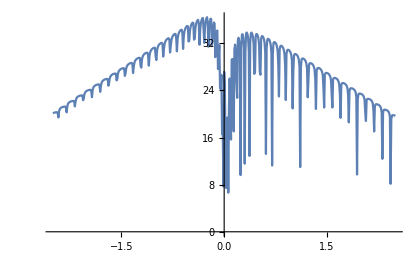

```mathematica
ListPlot[%36,Joined->True]
```

```mathematica
RandomInteger[{1,50}]
```

22

```mathematica
impu[ω_,δ_,t_,ϵ_,ϵ1_,m_]:= Inverse[Module[{κ=β[ω,0.0001,1,0,m],μ= RandomInteger[{1,50}]},ReplacePart[κ,{{μ,μ}}->ω+ⅈ*0.0001-ϵ1]]]
```

```mathematica
Table[{ω,Mean[ParallelTable[ca162[ω,0.5,50,0.0001,1,0],10000]]},{ω,Range[-2.5,2.5,0.5]}]
```

{{-2.5,20.1311},{-2.,23.9771},{-1.5,27.6909},{-1.,29.8129},{-0.5,34.1411},{0.,27.2301},{0.5,32.8413},{1.,20.8856},{1.5,26.9798},{2.,23.4161},{2.5,19.6864}}

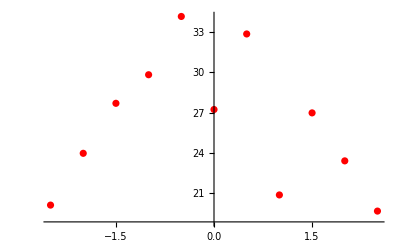

```mathematica
ListPlot[%43,PlotStyle->Red]
```

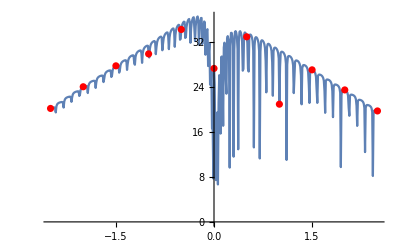

```mathematica
Show[%38,%45]
```

```mathematica
ConjugateTranspose[%37][[2]]//Around
```

20.8360.030

```mathematica
ca1[ω_,ϵ1_,m_,δ_,t_,ϵ_,n_]:=Module[{Tin=T[1,m],T1=T[1,m],list,b2},
b2=Module[{},list={RandomSample[Join[Table[impu[ω,δ,t,ϵ,ϵ1,m],n],Table[impu[ω,δ,t,ϵ,0,m],10-n]]]};
sl1= Module[{J=LEFT[ω,0.0001,1,0,m]},Do[J=Inverse[IdentityMatrix[m]-list[[1,ζ]].ConjugateTranspose[Tin].J.Tin].list[[1,ζ]],{ζ,1,10}];
 J=J];
Il1:=Inverse[IdentityMatrix[m]-sl1.T1.SL[ω,0.0001,1,0,m].T1].sl1;
Ir1:=Inverse[IdentityMatrix[m]-SL[ω,0.0001,1,0,m].T1.sl1.T1].SL[ω,0.0001,1,0,m];gdd1:=Il1-ConjugateTranspose[Il1];grr1:=Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SL[ω,0.0001,1,0,m].T1.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]>tr[ω,0.0001,1,0,m],tr[ω,0.0001,1,0,m],Abs[Tr[gdd1.T1.grr1.T1-T1.GNON1.T1.GNON1]]]];
b2]
```

```mathematica
ca1[0,0.5,50,0.0001,1,0,2]
```

42.801

```mathematica
Mean[ParallelTable[ca1[1,0.5,50,0.0001,1,0,1],10000]]
```

20.5212

```mathematica
Do[,{x,10}]
```

```mathematica
Table[{ω,RandomInteger[{1,ω}]},{ω,100}]
```

{{1,1},{2,2},{3,3},{4,1},{5,4},{6,6},{7,7},{8,3},{9,1},{10,5},{11,2},{12,3},{13,9},{14,6},{15,9},{16,12},{17,16},{18,1},{19,15},{20,17},{21,12},{22,3},{23,15},{24,6},{25,12},{26,22},{27,24},{28,20},{29,11},{30,24},{31,23},{32,21},{33,24},{34,23},{35,32},{36,10},{37,3},{38,27},{39,26},{40,22},{41,11},{42,3},{43,23},{44,32},{45,23},{46,8},{47,5},{48,17},{49,28},{50,48},{51,25},{52,20},{53,53},{54,54},{55,13},{56,36},{57,44},{58,15},{59,48},{60,39},{61,30},{62,6},{63,63},{64,53},{65,13},{66,34},{67,28},{68,15},{69,25},{70,69},{71,1},{72,34},{73,19},{74,21},{75,46},{76,48},{77,66},{78,65},{79,10},{80,20},{81,51},{82,5},{83,21},{84,45},{85,44},{86,51},{87,72},{88,86},{89,72},{90,44},{91,69},{92,67},{93,70},{94,93},{95,77},{96,5},{97,88},{98,40},{99,14},{100,97}}

```mathematica
F[x_]:=ParallelTable[{ω,Mean[Table[RandomReal[{0,x}],10000]]},{ω,Range[-2.5,2.5,0.01]}]
```

```mathematica
Do[Export["/home/shardulmukim/PhD/PRL-short/test"<>ToString[x]<>".dat",Table[{ω,Mean[ParallelTable[ca1[ω,0.5,50,0.0001,1,0,x],10000]]},{ω,Range[-2.5,2.5,0.01]}]],{x,5}]
```

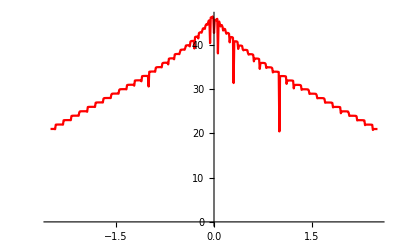

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/PRL-short/test1.dat"],PlotStyle->Red]
```

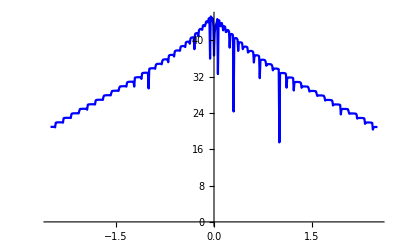

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/PRL-short/test2.dat"],PlotStyle->Blue]
```

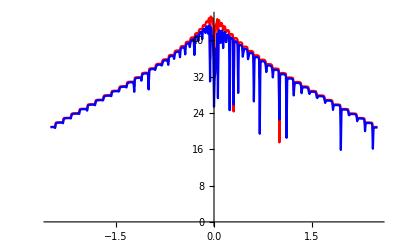

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/PhD/PRL-short/test2.dat"],PlotStyle->Red],ListLinePlot[Import["/home/shardulmukim/PhD/PRL-short/test5.dat"],PlotStyle->Blue]]
```